# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\Late time ensembles\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];

Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[Total[N[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];
Clear[sur];
sur[eigenval_,eigenvec_,ini_,t_]:=Module[{psit,phases=arrayt[t,eigenval,eigenvec],ck=Conjugate[eigenvec].ini},
Abs[Conjugate[Total[N[ck*phases]]].ini]^2
];
Clear[ExpandBlockVector];
ExpandBlockVector[v_,map_,type_,L_]:=Module[{full=ConstantArray[0,2^L],k=1,a,b,coeff},
Do[
If[Length[pair]==1,full[[pair[[1]]+1]]=v[[k]],{a,b}=pair;
coeff=v[[k]]/Sqrt[2];
If[type=="even",full[[a+1]]=coeff;full[[b+1]]=coeff,full[[a+1]]=coeff;full[[b+1]]=-coeff];];
k++,{pair,map}];
full];
Clear[revIndex];
revIndex[i_,L_]:=FromDigits[Reverse[IntegerDigits[i,2,L]],2];

Unfold[eigenvalues_List] := 
Module[
	{skd, unfolded, n, smoothCDF, smoothPDF},
	
	n=Length[eigenvalues];
	
	(*Create smooth kernel distribution for the CDF*)
	skd=SmoothKernelDistribution[eigenvalues, "StandardGaussian", {
		"Bounded", {Min[eigenvalues], Max[eigenvalues]}, "Gaussian"
		}];
		
	(*Unfold:ε_i=N*CDF(E_i)*)
	unfolded = Table[ n*CDF[skd, eigenvalues[[i]]], {i,n}];
	
	(*Define the smooth functions*)
	smoothCDF=Function[x,n*CDF[skd,x]];
	smoothPDF=Function[x,n*PDF[skd,x]];
	
	(*Return unfolded spectrum and related functions*)
	<|"UnfoldedLevels"->unfolded,
	"SmoothCDF"->smoothCDF,(*Cumulative:N(E)*)
	"SmoothPDF"->smoothPDF,(*Density:ρ(E)*)
	"Bandwidth"->skd["Bandwidth"],
	"OriginalLevels"->eigenvalues(*Useful for comparison*)|>
]
```

# RPS initial states

```mathematica
J=1;
h=1;
```

```mathematica
L=12;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
g=0.5;
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],50];
```

```mathematica
cks=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
ipr=ParallelTable[Total[Abs[j]^4],{j,cks}];
```

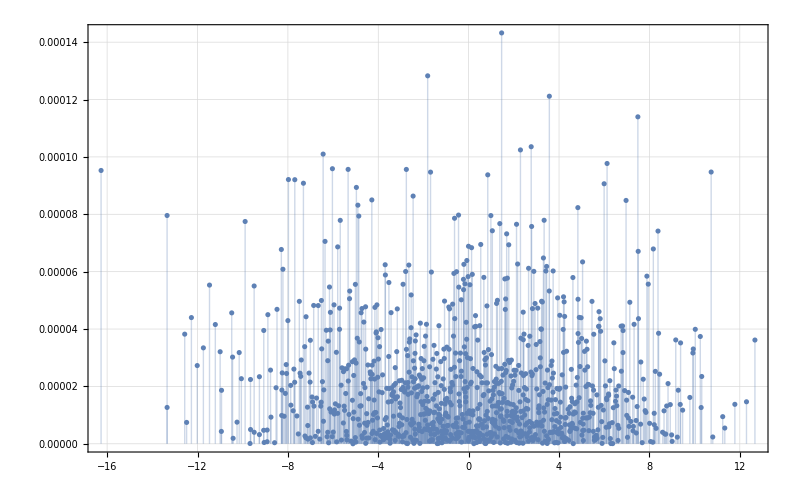

```mathematica
ListPlot[Transpose[{allvals,Abs[Mean[cks]]^2}],PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Filling->Bottom]
```

# Svn

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,3,0.0025}];
tlist//Length
```

1601

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],1000];
```

```mathematica
productstatesfull=Table[haar[L],500];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],1000];
```

```mathematica
neelState[L_]:=Module[{spins},spins=Table[If[OddQ[i],qubit[0,0],(* |↑⟩ on odd sites*)qubit[Pi,0]    (* |↓⟩ on even sites*)],{i,1,L}];
Flatten[KroneckerProduct@@spins]];
```

```mathematica
neelStatex[L_]:=Module[{spins},spins=Table[If[OddQ[i],qubit[Pi/2,0],(* |↑⟩ on odd sites*)qubit[Pi/2,Pi]    (* |↓⟩ on even sites*)],{i,1,L}];
Flatten[KroneckerProduct@@spins]];
```

```mathematica
(*DistributeDefinitions[evolvers,productstatesfull,new];*)
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

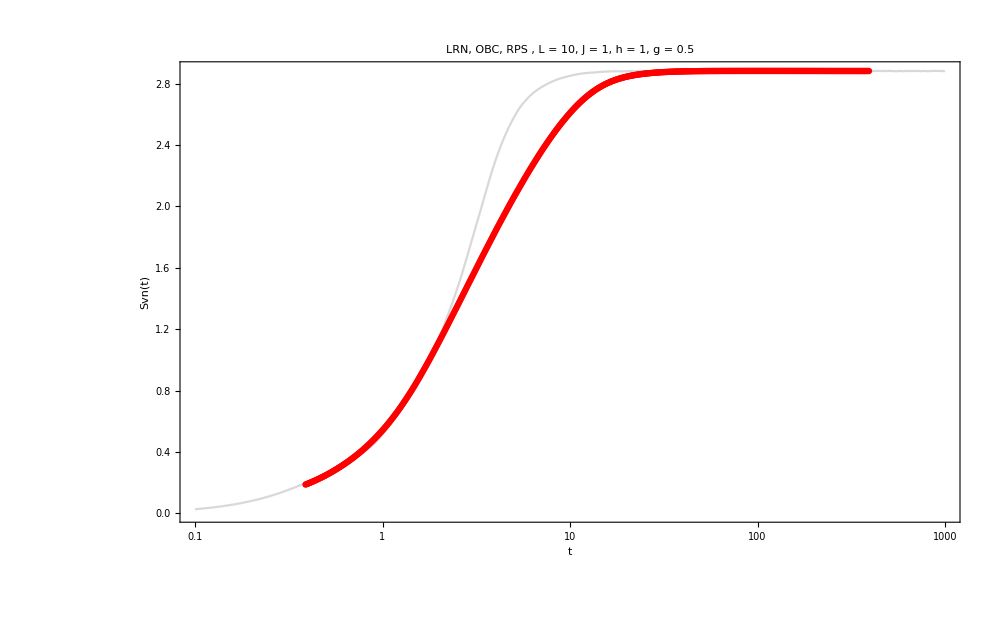

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

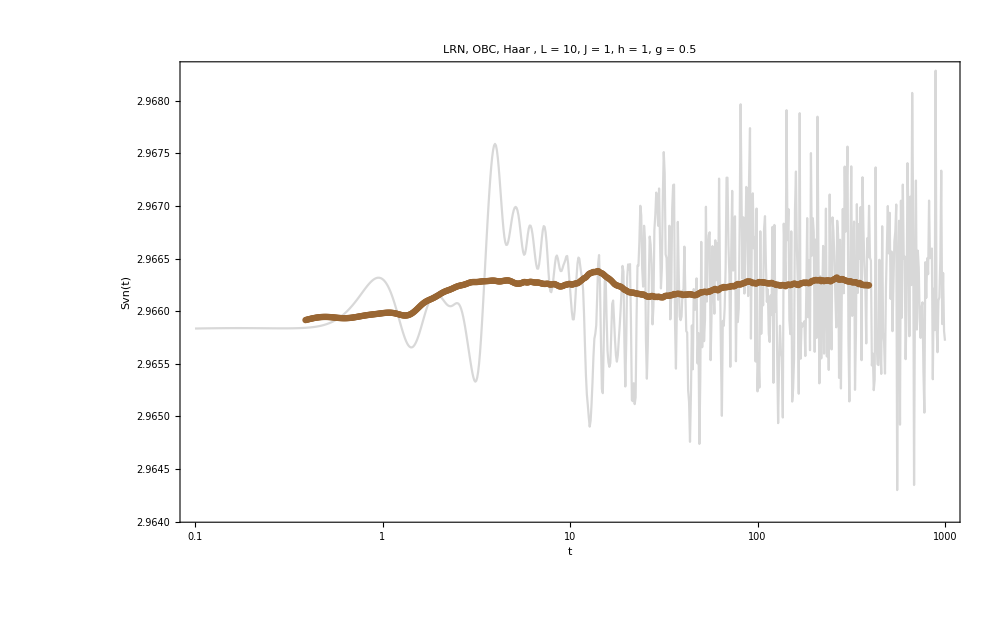

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Brown,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

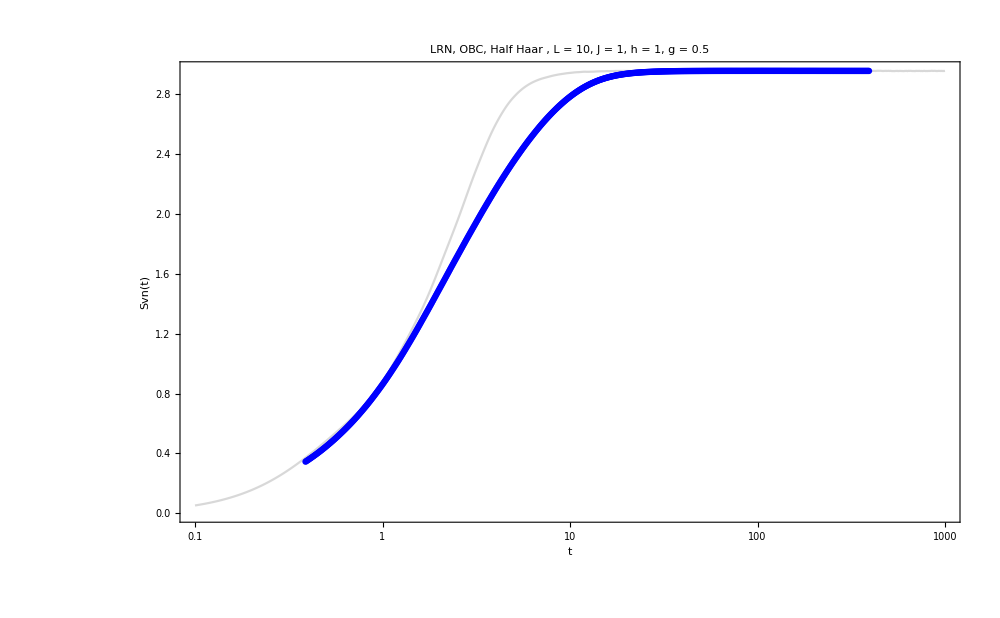

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Blue,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

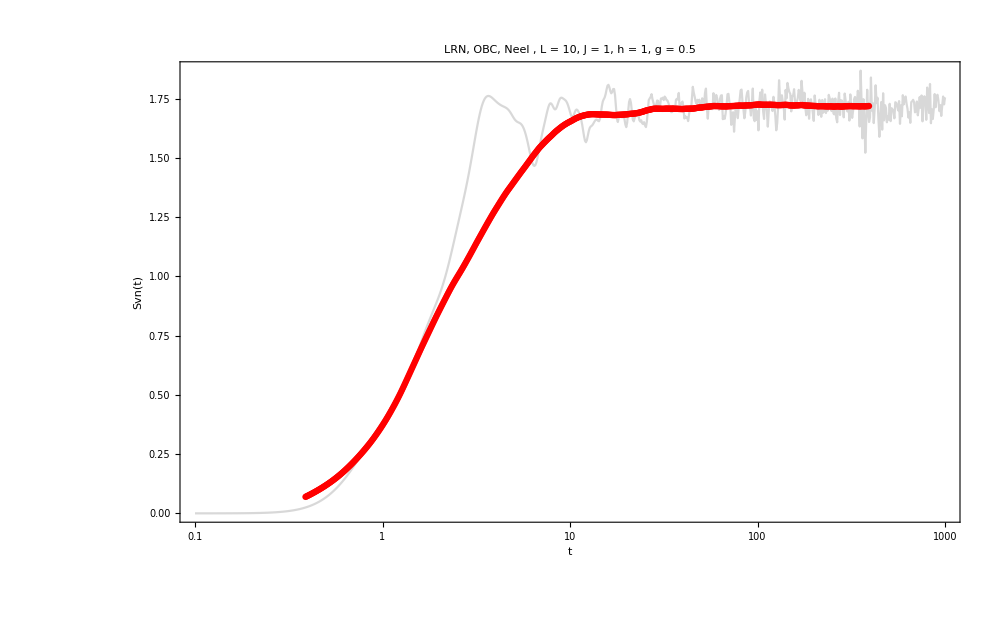

```mathematica
ListLogLinearPlot[{Transpose[{tlist,dataneel}],MovingAverage[Transpose[{tlist,dataneel}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Neel , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

```mathematica
tlist=Table[i,{i,1000,1100,0.2}];
tlist//Length
```

501

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
dataneel=Module[{evolFunc=evolvers},
With[{final=evolFunc[coherentstate[qubit[Pi/2,Pi/2],L]]},
Map[new,Transpose[final]]]];
```

```mathematica
finalneel=Table[i,{i,dataneel}];
{bins,heights}=HistogramList[finalneel,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

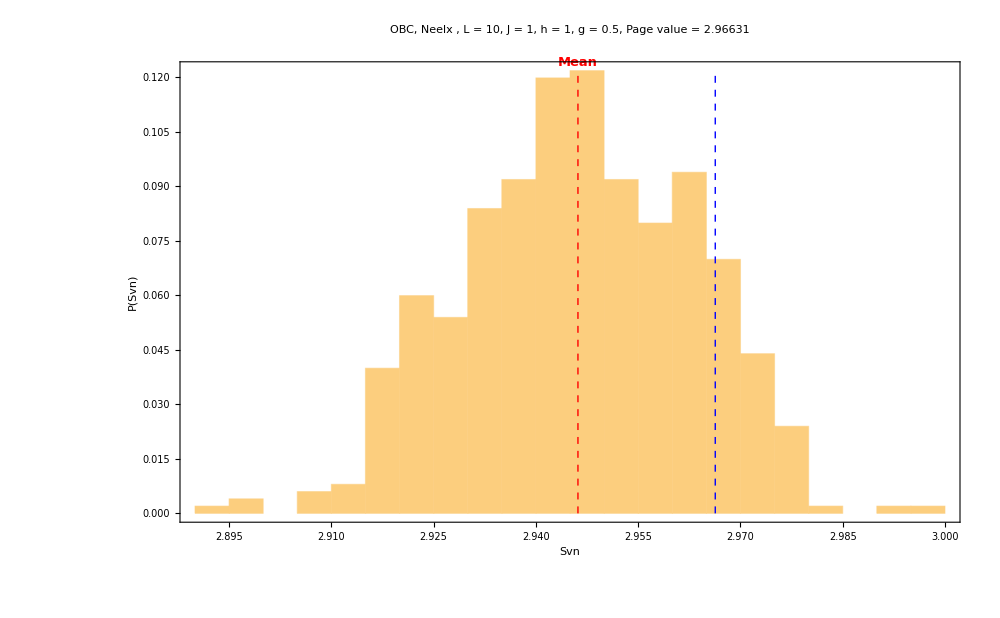

```mathematica
neeldis=Histogram[finalneel,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Neelx , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g]<>", Page value = "<>ToString[N[pageEntropy[L/2.,L/2.]]],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->1000,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalneel],0},{Mean[finalneel],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalneel],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

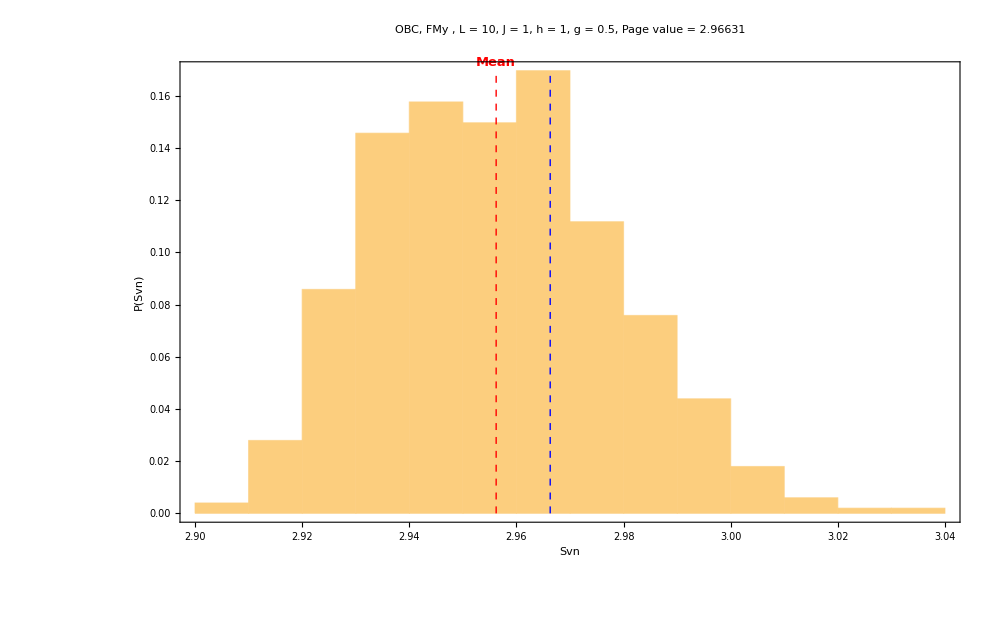

```mathematica
neeldis=Histogram[finalneel,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, FMy , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g]<>", Page value = "<>ToString[N[pageEntropy[L/2.,L/2.]]],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->1000,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalneel],0},{Mean[finalneel],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalneel],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

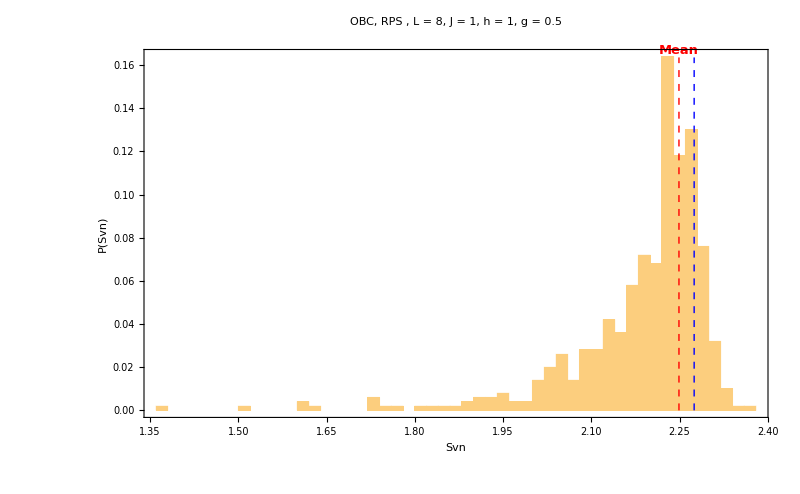

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

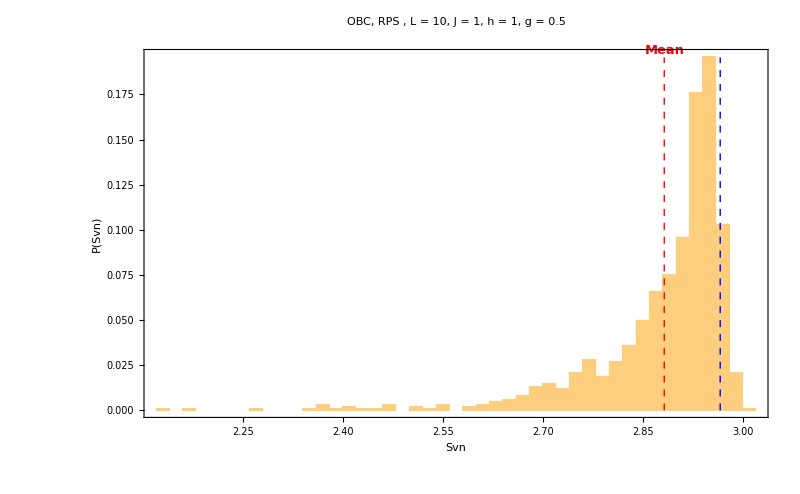

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

```mathematica
finalhalfhaar=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalhalfhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

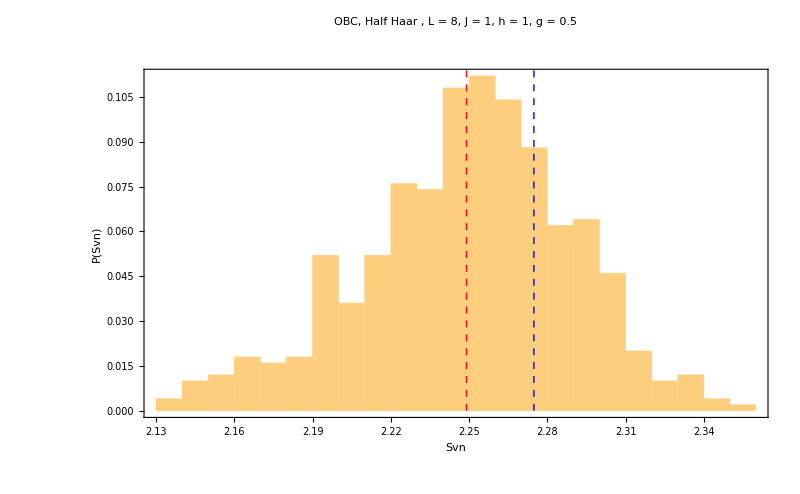

```mathematica
halfhaardis=Histogram[finalhalfhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.97},{-1,0}]}]
```

```mathematica
finalhalfhaar=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalhalfhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

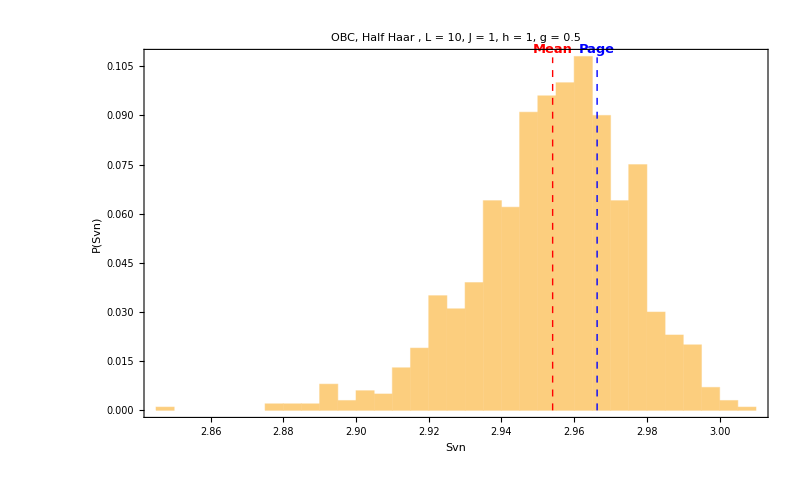

```mathematica
halfhaardis=Histogram[finalhalfhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.97},{-1,0}]},PlotRange->All]
```

```mathematica
finalhaar=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

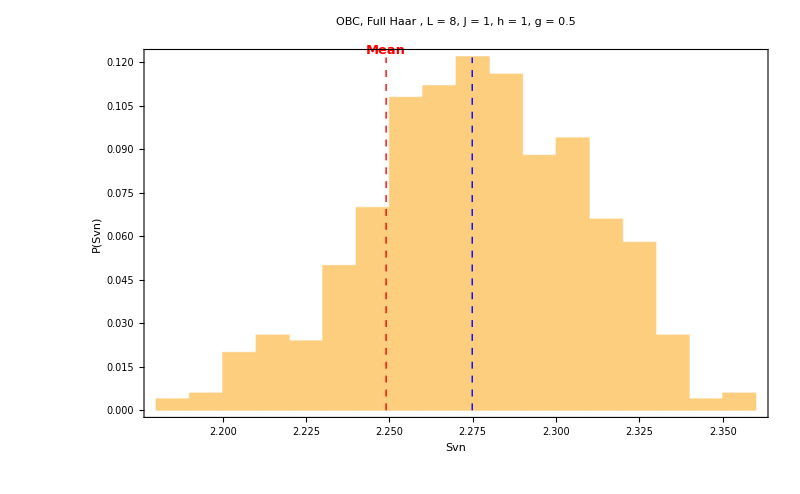

```mathematica
fullhaardis=Histogram[finalhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Full Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]}]
```

```mathematica
finalhaar=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

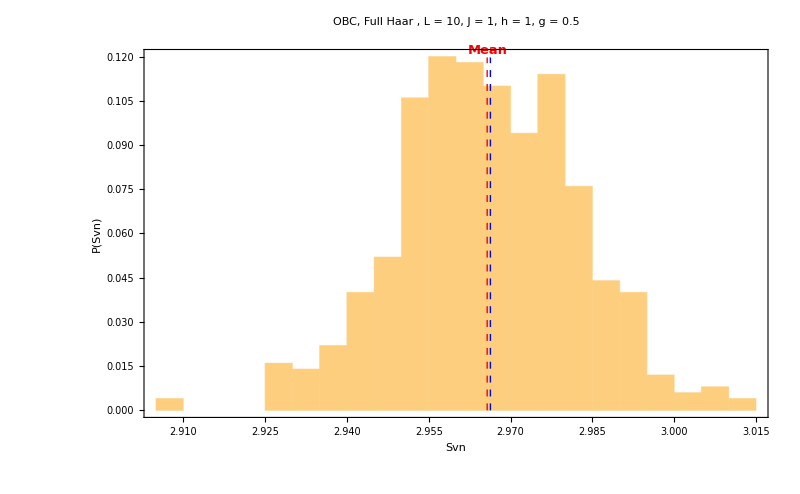

```mathematica
fullhaardis=Histogram[finalhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Full Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhaar],0},{Mean[finalhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]}]
```

```mathematica
pageEntropy[16/2.,16/2.]
```

5.04519

# Svn, 1 single state

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[i,{i,0,2000,0.5}];
tlist//Length
```

4001

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
productstatesfull=RandomChainProductState[L];
```

```mathematica
productstatesfull=haar[L];
```

```mathematica
productstatesfull=Flatten[KroneckerProduct[haar[L/2],haar[L/2]]];
```

```mathematica
neelState[L_]:=Module[{spins},spins=Table[If[OddQ[i],qubit[0,0],(* |↑⟩ on odd sites*)qubit[Pi,0]    (* |↓⟩ on even sites*)],{i,1,L}];
Flatten[KroneckerProduct@@spins]];
```

```mathematica
neelStatex[L_]:=Module[{spins},spins=Table[If[OddQ[i],qubit[Pi/2,0],(* |↑⟩ on odd sites*)qubit[Pi/2,Pi]    (* |↓⟩ on even sites*)],{i,1,L}];
Flatten[KroneckerProduct@@spins]];
```

```mathematica
(*DistributeDefinitions[evolvers,productstatesfull,new];*)
```

```mathematica
data=Module[{evolFunc=evolvers},
With[{final=evolFunc[productstatesfull]},
Map[new,Transpose[final]]]];
```

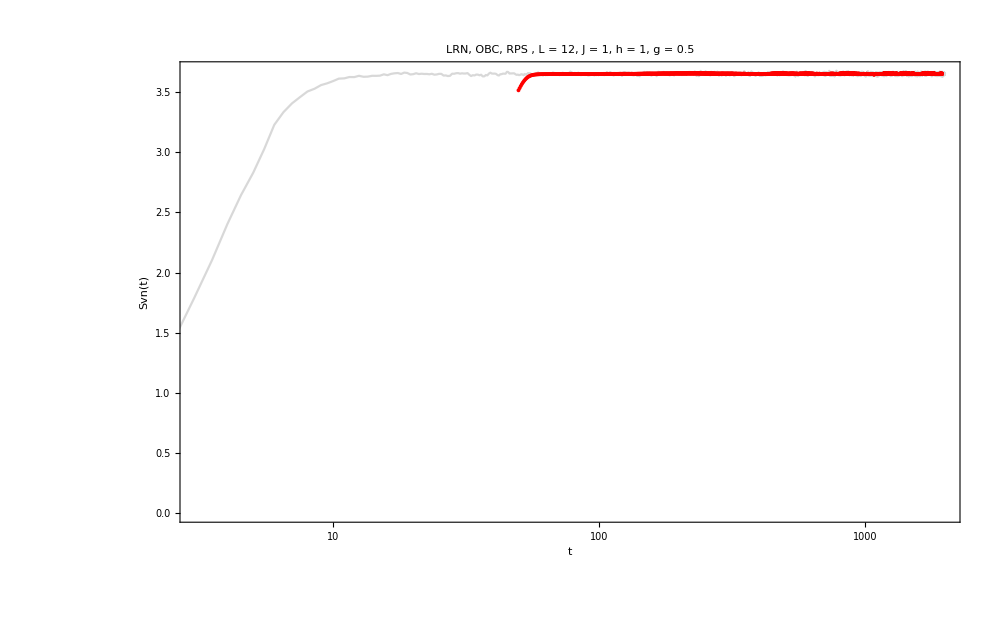

```mathematica
ListLogLinearPlot[{Transpose[{tlist,data}],MovingAverage[Transpose[{tlist,data}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

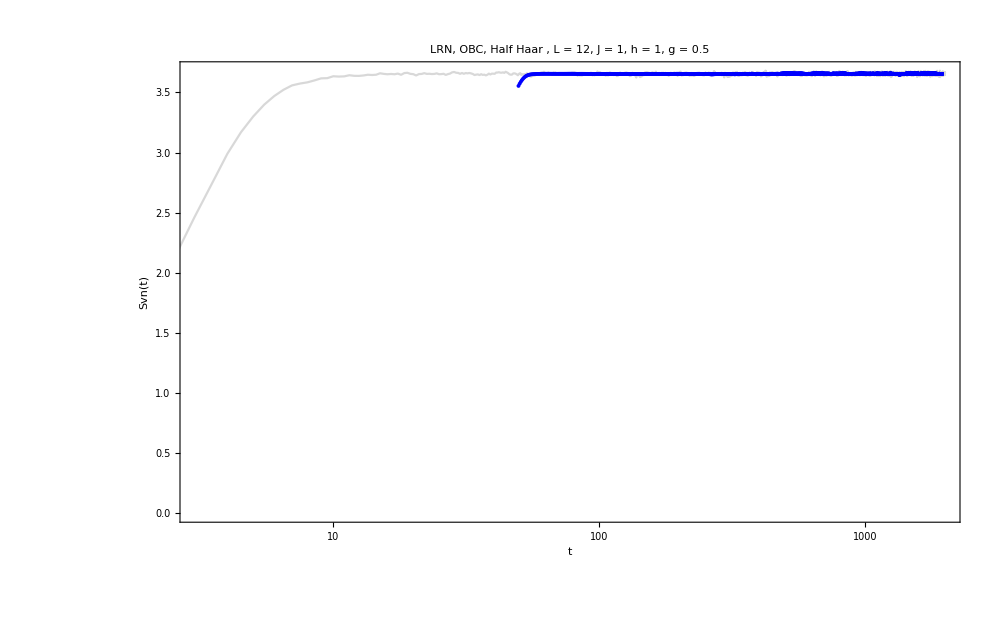

```mathematica
ListLogLinearPlot[{Transpose[{tlist,data}],MovingAverage[Transpose[{tlist,data}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Blue,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

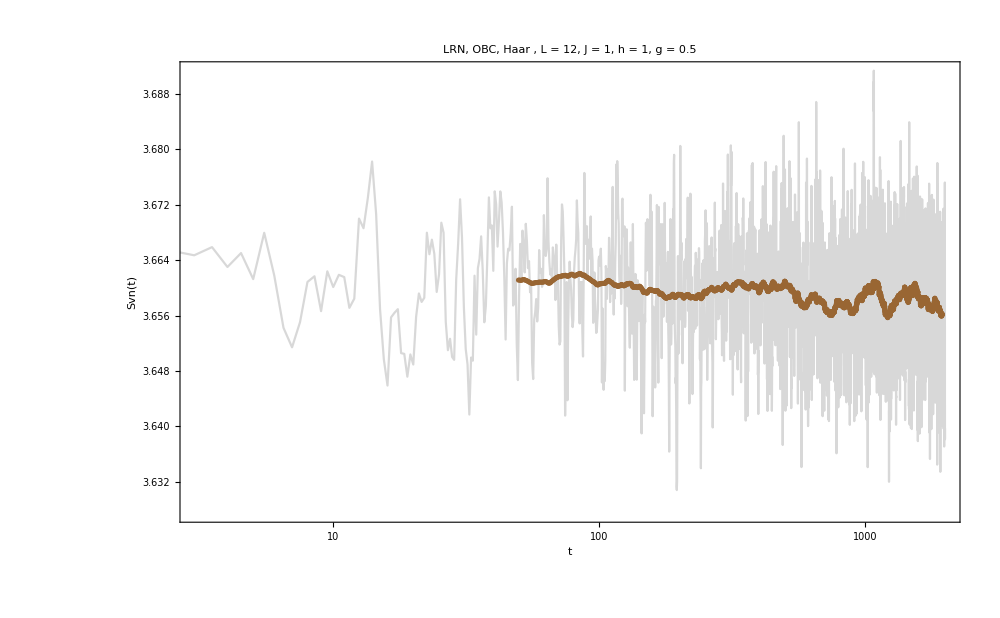

```mathematica
ListLogLinearPlot[{Transpose[{tlist,data}],MovingAverage[Transpose[{tlist,data}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Brown,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

```mathematica
finalrps=Table[i,{i,data[[-1000;;-1]]}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

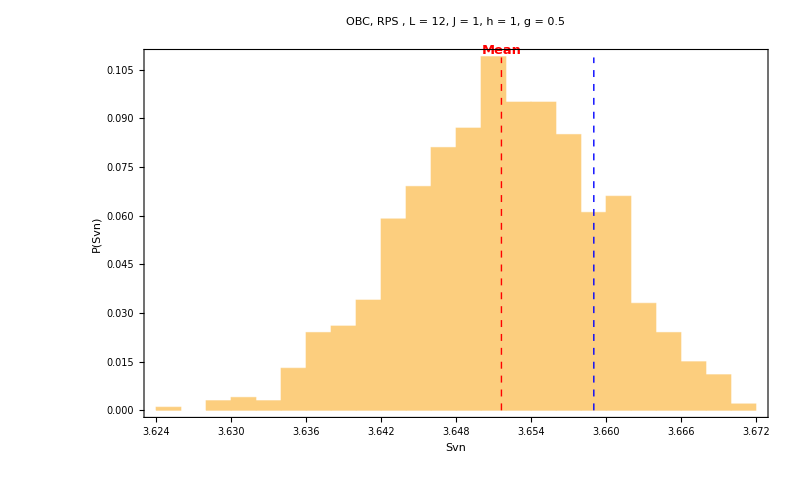

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

```mathematica
finalhalfhaar=Table[i,{i,data[[-1000;;-1]]}];
{bins,heights}=HistogramList[finalhalfhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

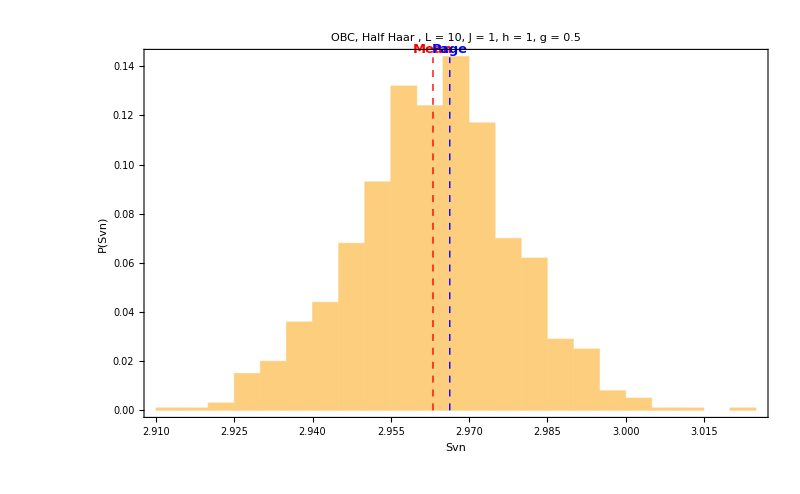

```mathematica
halfhaardis=Histogram[finalhalfhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.97},{-1,0}]}]
```

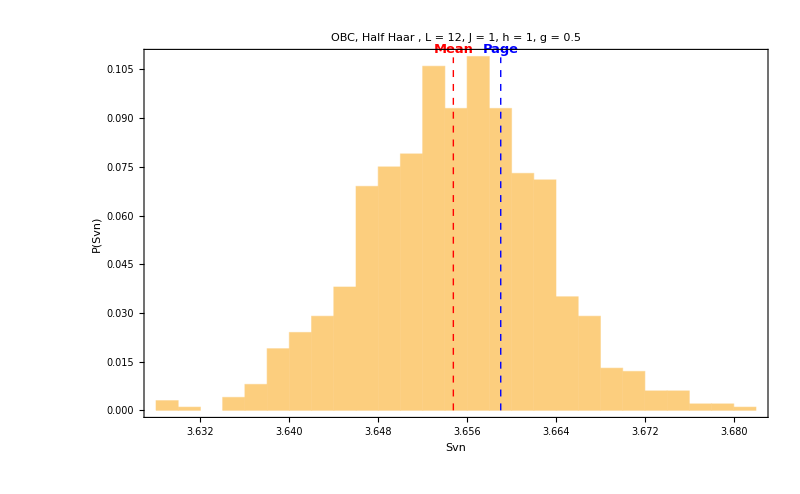

```mathematica
halfhaardis=Histogram[finalhalfhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.97},{-1,0}]}]
```

```mathematica
finalhaar=Table[i,{i,data[[-1000;;-1]]}];
{bins,heights}=HistogramList[finalhaar,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

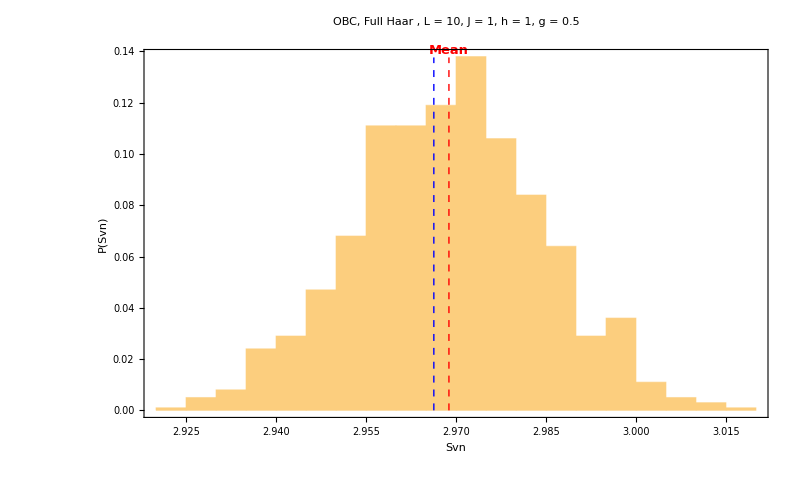

```mathematica
fullhaardis=Histogram[finalhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Full Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhaar],0},{Mean[finalhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]}]
```

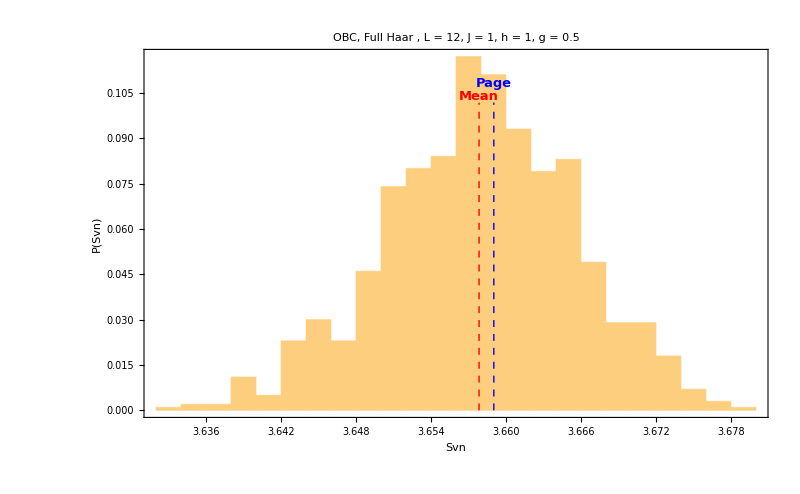

```mathematica
fullhaardis=Histogram[finalhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Full Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhaar],0},{Mean[finalhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhaar],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]}]
```

## Other states

```mathematica
ListLogLinearPlot[{Transpose[{tlist,dataneel}],MovingAverage[Transpose[{tlist,dataneel}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Neel , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

-Graphics-

```mathematica
finalneel=Table[i,{i,dataneel}];
{bins,heights}=HistogramList[finalneel,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

```mathematica
neeldis=Histogram[finalneel,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Neelx , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g]<>", Page value = "<>ToString[N[pageEntropy[L/2.,L/2.]]],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->1000,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalneel],0},{Mean[finalneel],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalneel],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

-Graphics-

```mathematica
neeldis=Histogram[finalneel,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, FMy , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g]<>", Page value = "<>ToString[N[pageEntropy[L/2.,L/2.]]],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->1000,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalneel],0},{Mean[finalneel],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalneel],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

-Graphics-

# Survival

```mathematica
productstatesfull=Table[haar[L],50];
```

```mathematica
productstatesfull={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[productstatesfull,evenini];
,{i,50}];
```

Table::nliter: Non-list iterator L/2 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

```mathematica
productstatesfull=Table[RandomChainProductState[L],50];
```

```mathematica
phasesAll=ParallelTable[Exp[-I*Outer[Times,allvalues[[h]],tlist]],{h,Length[hlist]}];
```

```mathematica
Clear[csurTime];
csurTime=Compile[{{phases,_Complex,2},{ck,_Complex,1}},Abs[(Abs[ck]^2).phases]^2,CompilationTarget->"WVM"];
Clear[compiledSurvival];
compiledSurvival[h_]:=Module[{phases=phasesAll[[h]]},Compile[{{ck,_Complex,1}},Abs[(Abs[ck]^2).phases]^2,CompilationTarget->"WVM"]];
```

```mathematica
plots={};
Do[

f1=compiledSurvival[h];
cks=ParallelTable[Conjugate[allvectors[[h]].j],{j,productstatesfull}];
test2=Map[f1[#]&,cks];
ipr=ParallelTable[Total[Abs[j]^4],{j,cks}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,Mean[test2]}],MovingAverage[Transpose[{tlist,Mean[test2]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-4,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Even RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}];
AppendTo[plots,plot];

,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

ListAnimate[{},AnimationRunning→False]

# LRN, RPS entanglement distribution

```mathematica
J=1;
h=1;
```

```mathematica
L=10;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
g=0.1;
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],100];
```

```mathematica
cks=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
ipr=ParallelTable[Total[Abs[j]^4],{j,cks}];
```

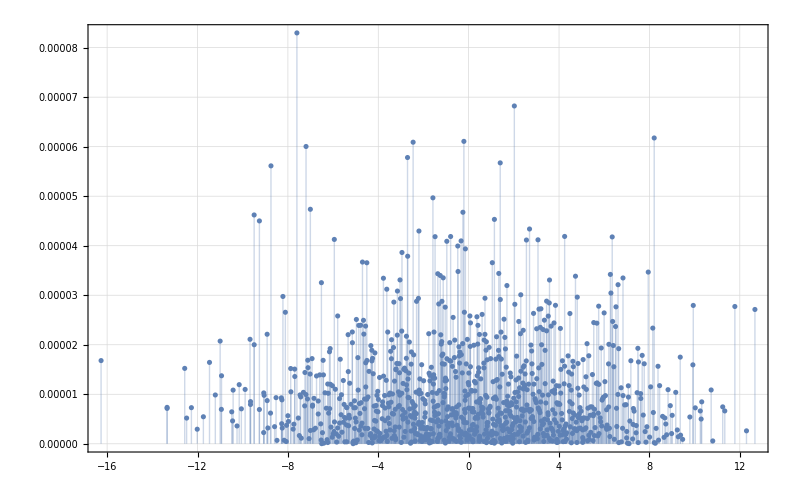

```mathematica
ListPlot[Transpose[{allvals,Abs[Mean[cks]]^2}],PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Filling->Bottom]
```

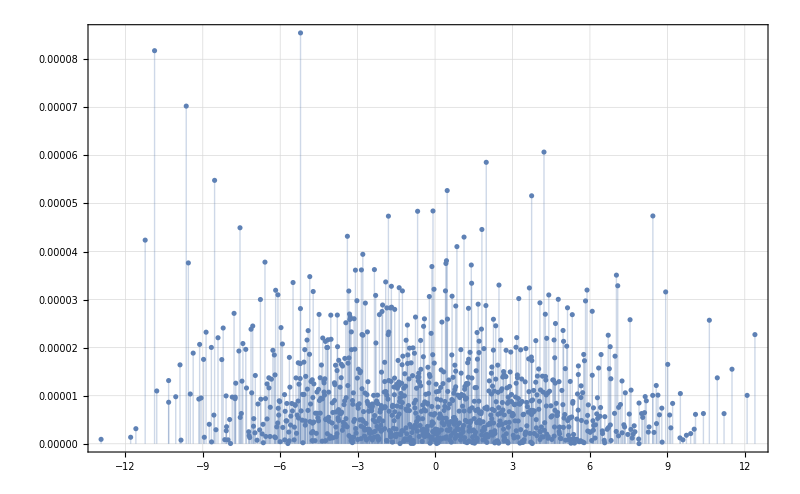

```mathematica
ListPlot[Transpose[{allvals,Abs[Mean[cks]]^2}],PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Filling->Bottom]
```

## P(Svn)

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,4,0.0025}];
tlist//Length
```

2001

```mathematica
productstatesfull=Table[RandomChainProductState[L],500];
```

```mathematica
g=0.001;
Ha=IsingHamiltonian[1,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

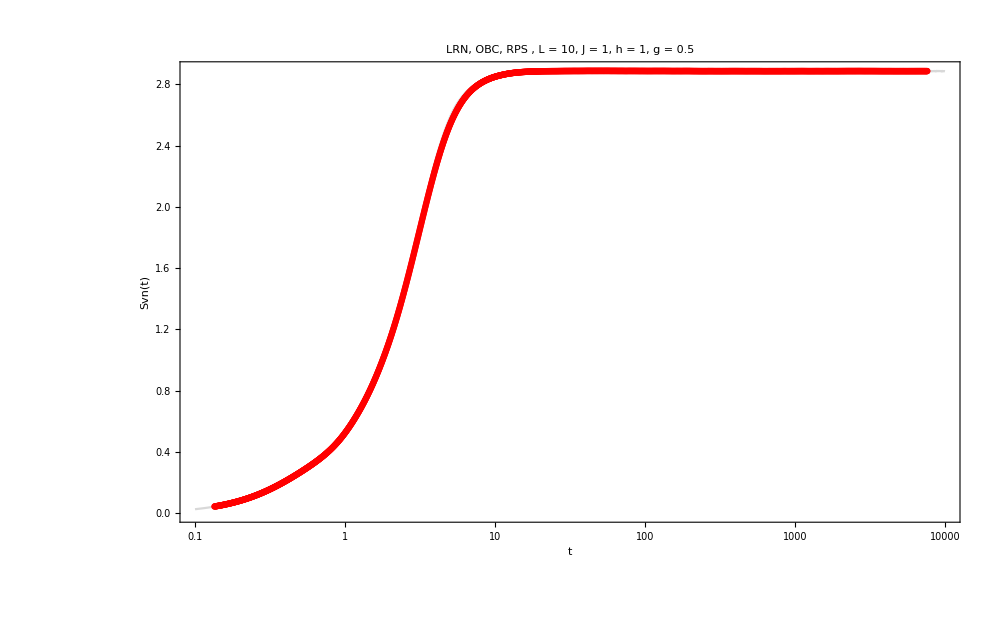

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

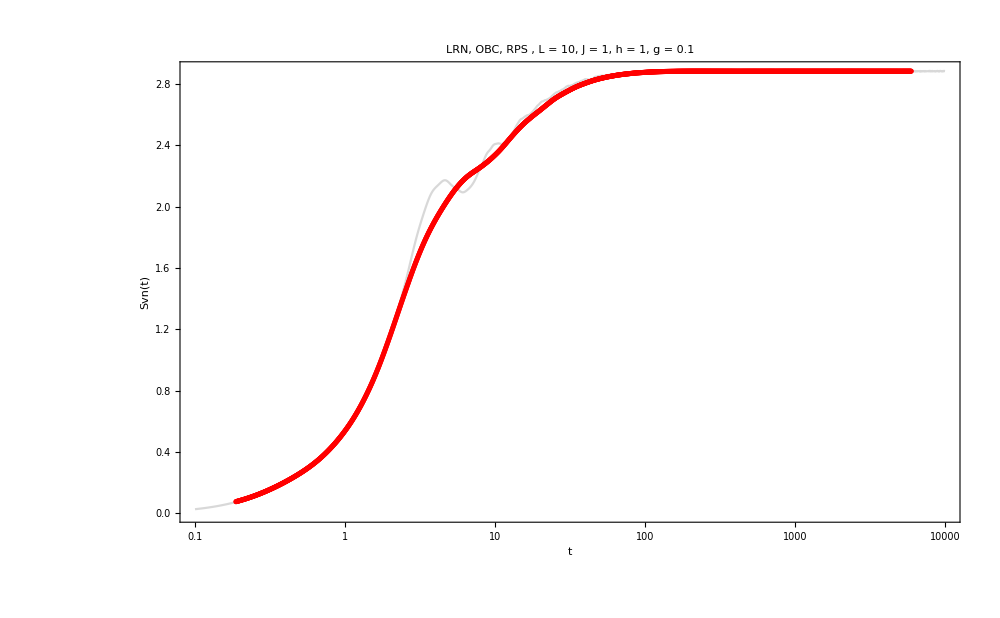

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

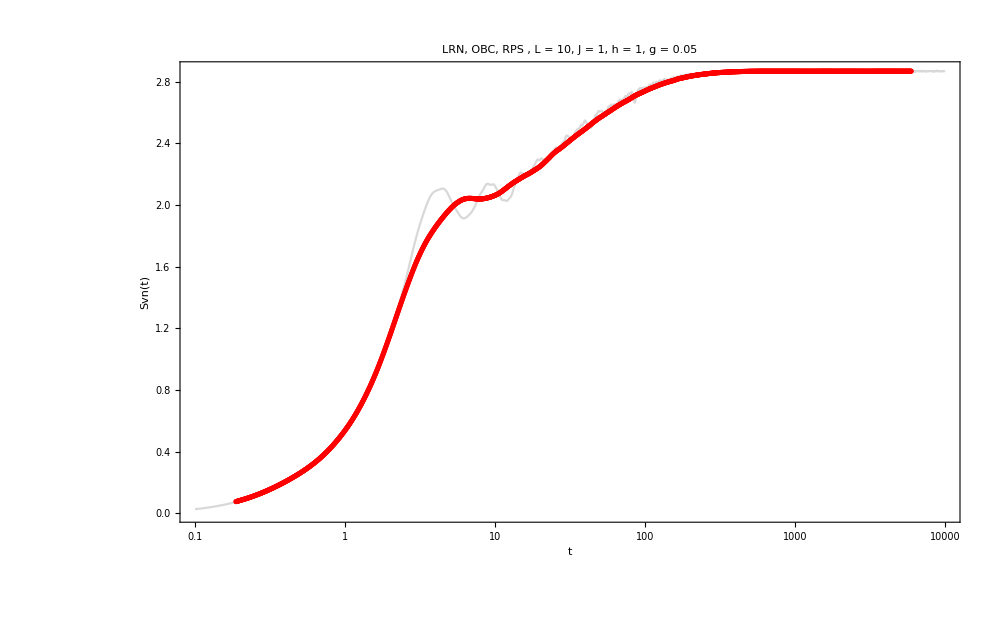

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

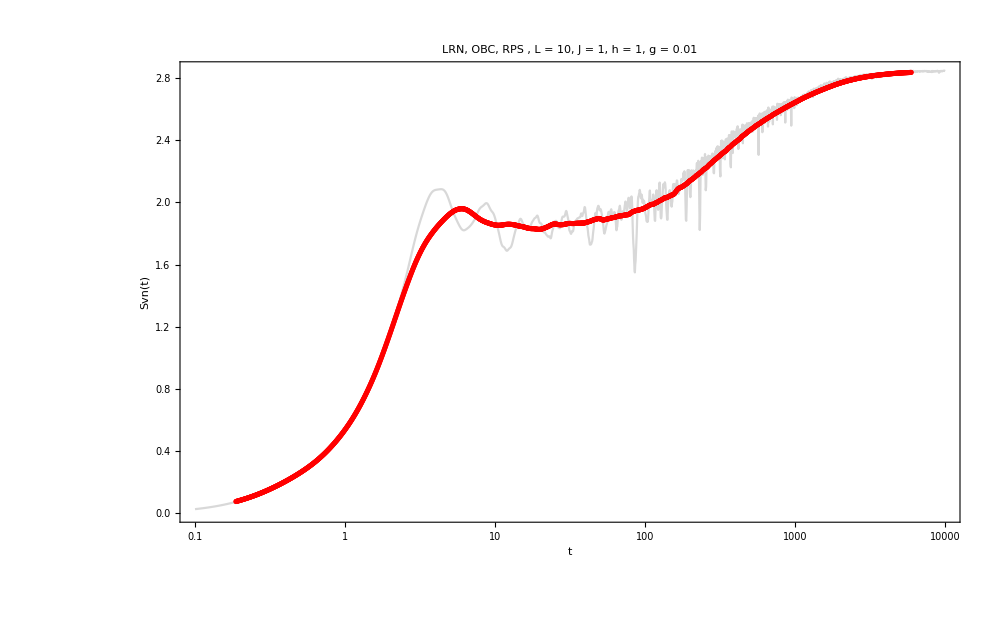

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

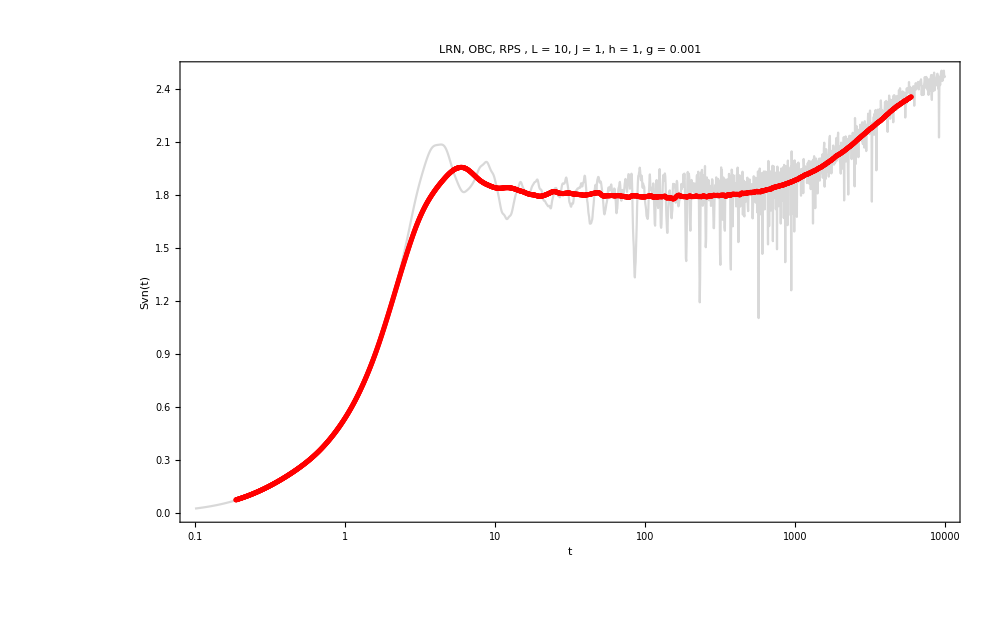

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

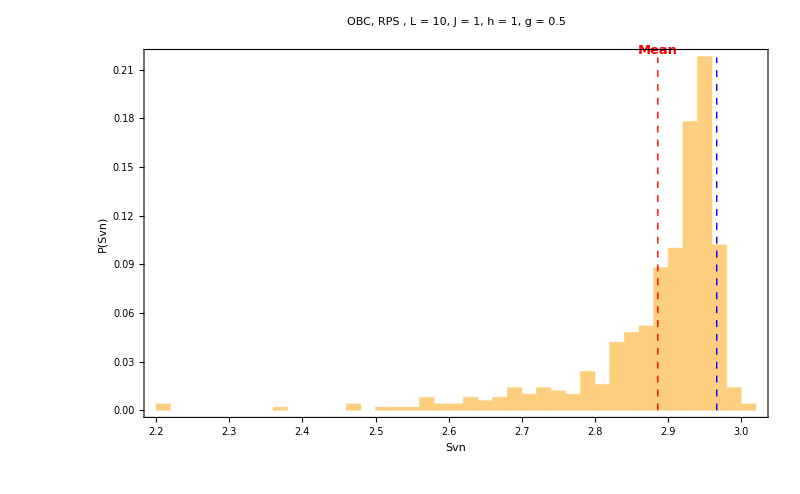

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

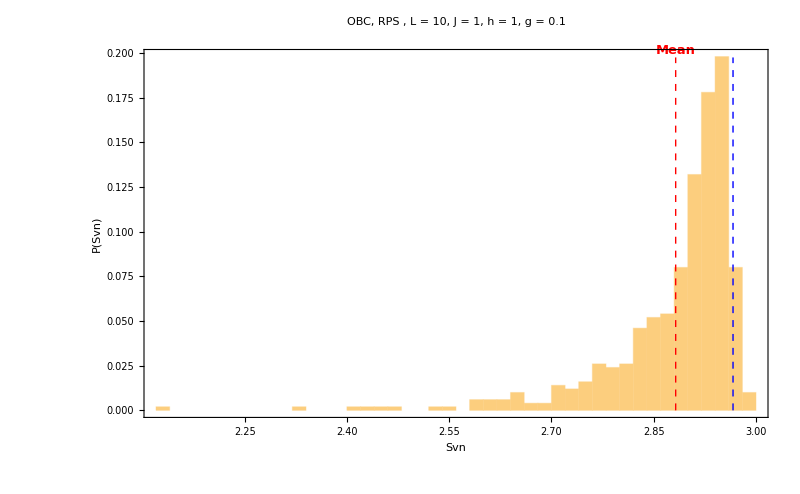

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

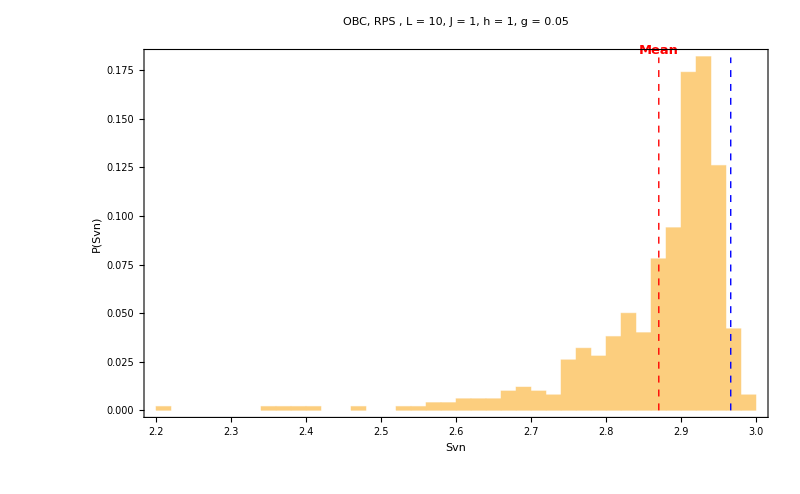

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

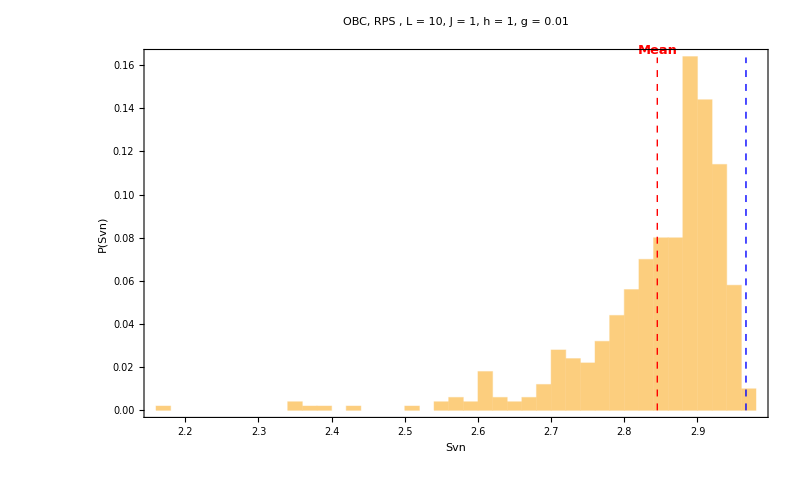

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

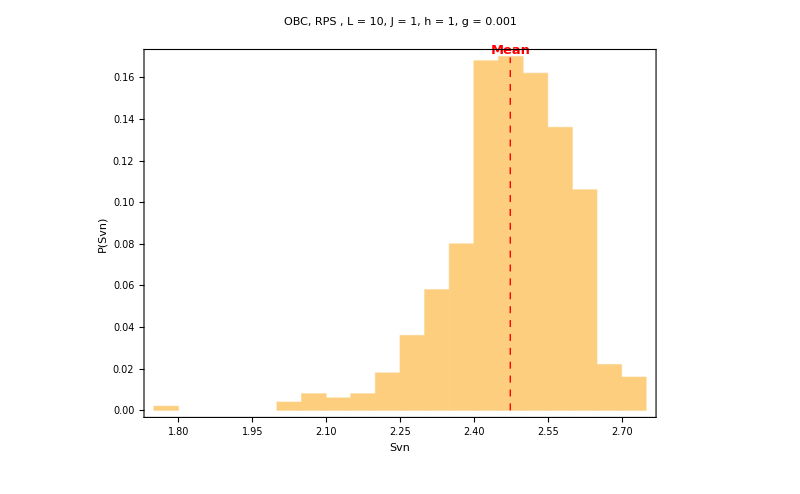

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

# SRN, RPS entanglement distribution

```mathematica
J=1;
g=1;
```

```mathematica
L=10;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
h=1.;
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],100];
```

```mathematica
cks=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
ipr=ParallelTable[Total[Abs[j]^4],{j,cks}];
```

```mathematica
ListPlot[Transpose[{allvals,Abs[Mean[cks]]^2}],PlotRange->All,ImageSize->800,PlotTheme->"Detailed",Filling->Bottom]
```

## P(Svn)

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,4,0.0025}];
tlist//Length
```

2001

```mathematica
productstatesfull=Table[RandomChainProductState[L],500];
```

```mathematica
h=0.1;
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

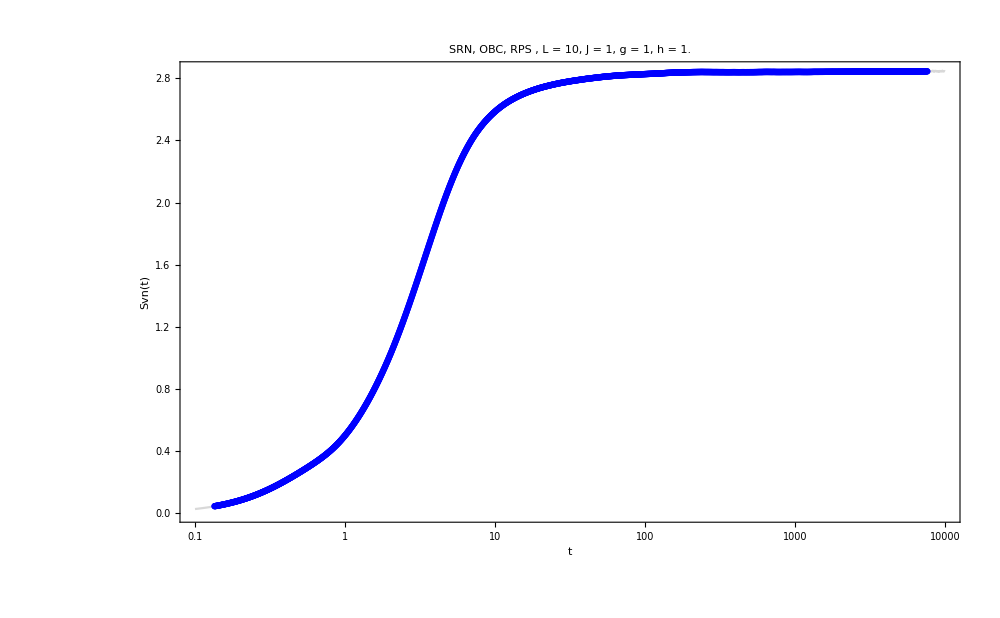

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Blue,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[h],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

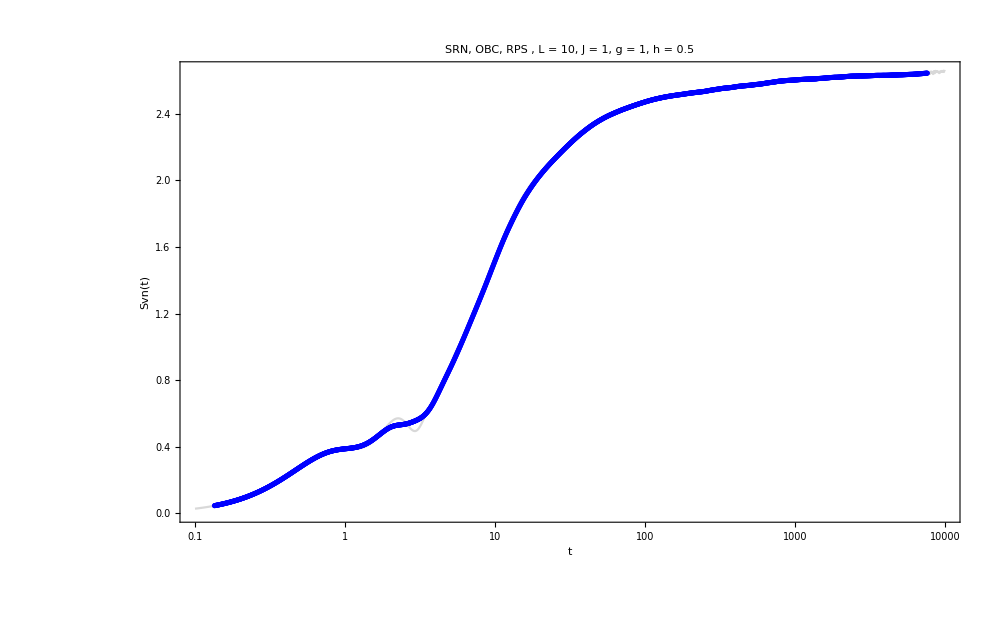

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Blue,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[h],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

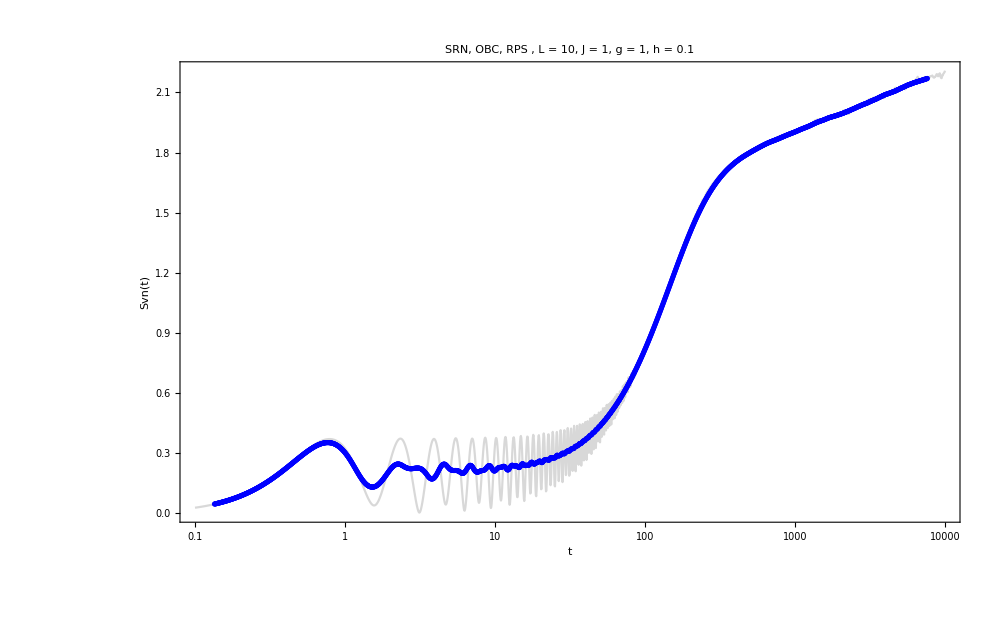

```mathematica
ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[Blue,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[h],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.05*Max[heights];   (*5% taller than tallest bin*)
```

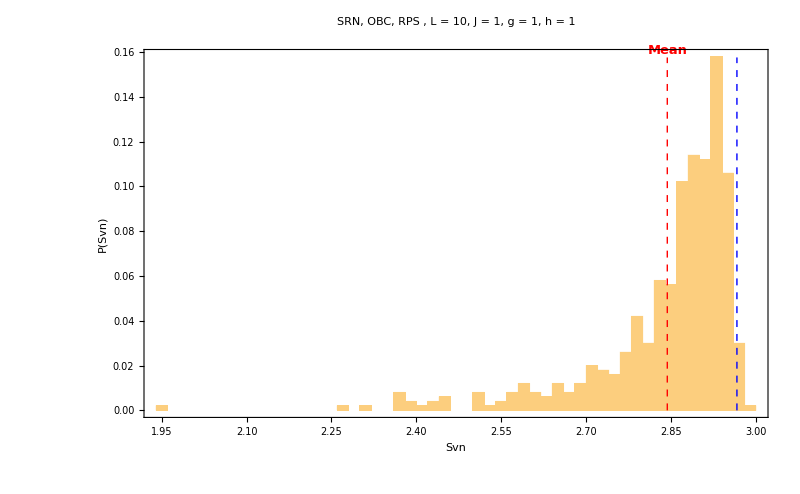

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

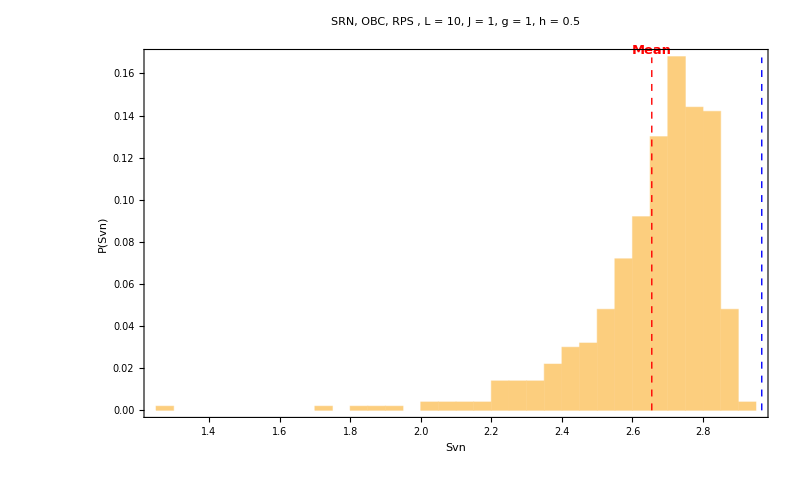

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[h],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

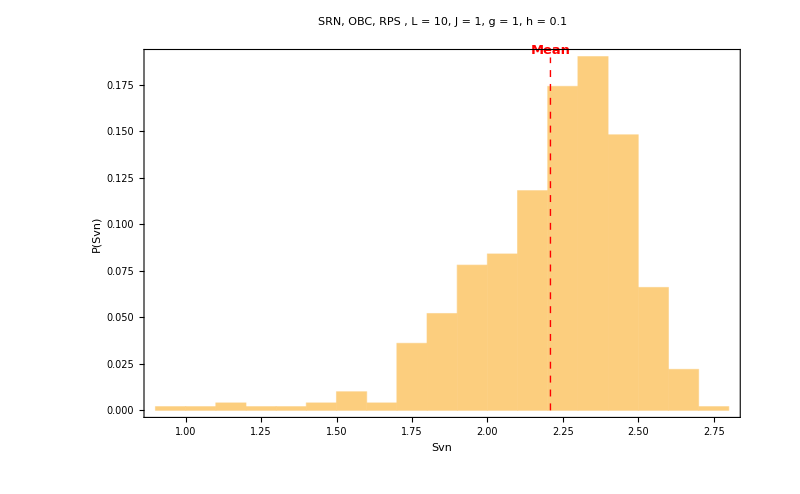

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["SRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 1, h = "<>ToString[h],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.97},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*1.01},{-1,0}]},PlotRange->All]
```

# RPS entanglement distribution & diagonal entropy

```mathematica
J=1;
h=1;
```

```mathematica
L=12;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
g=0.5;
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
```

```mathematica
neweven=ParallelTable[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=ParallelTable[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

## P(Svn) RPS, h = 1, g = 0.5

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,10,0.0020}];
tlist//Length
```

5501

```mathematica
productstatesfull=Table[RandomChainProductState[L],1000];
```

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
(*DistributeDefinitions[evolvers,productstatesfull,new];*)
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

$Aborted

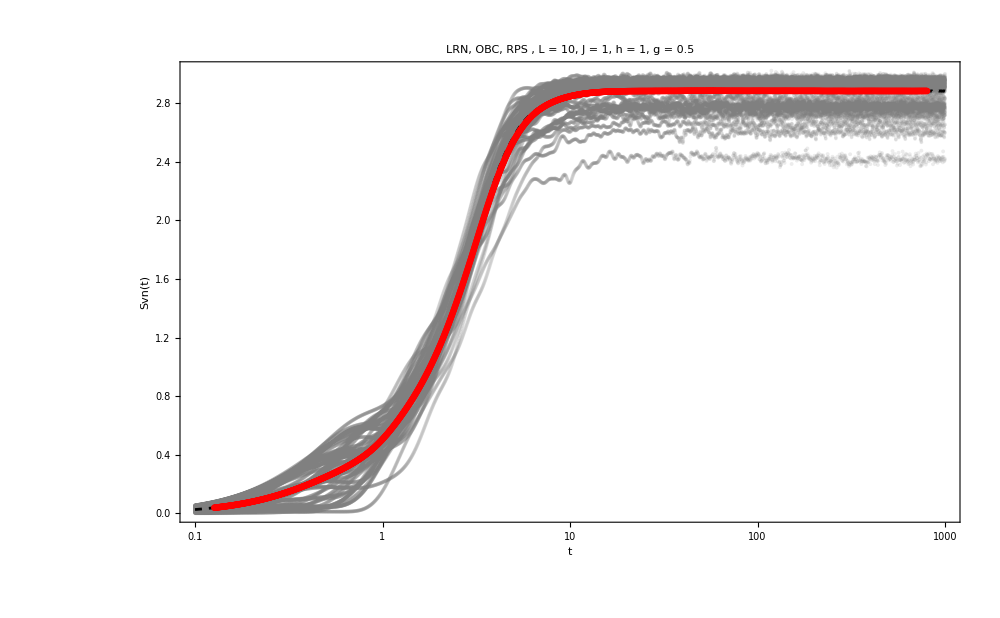

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

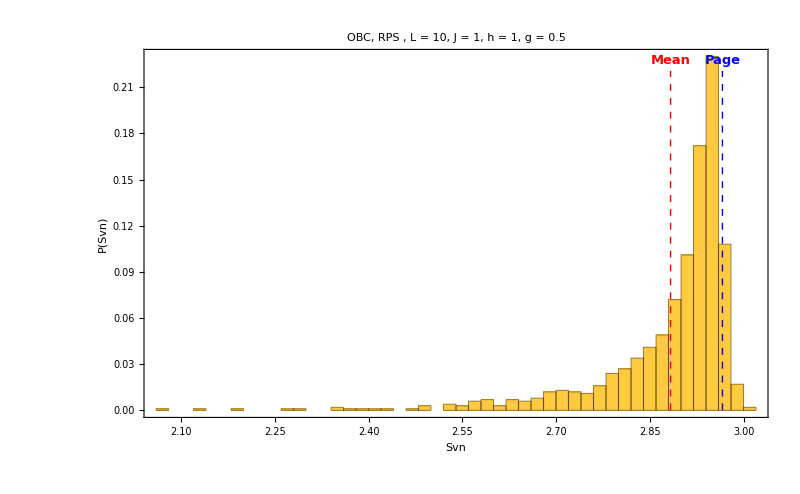

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
states=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
```

```mathematica
sdiagonal=ParallelTable[With[{M=ArrayReshape[j,{2^(L/2),2^(L/2)}]},Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]],{j,states}];
```

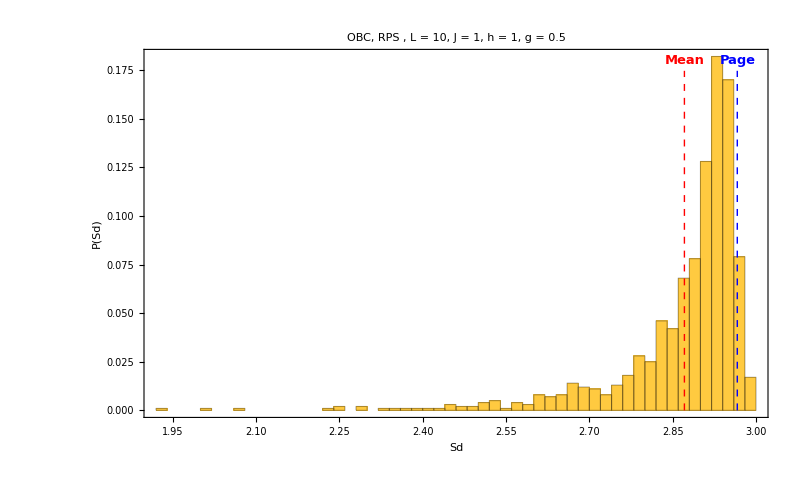

```mathematica
{bins,heights}=HistogramList[sdiagonal,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[sdiagonal,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Sd",25,Black],Style["P(Sd)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[sdiagonal],0},{Mean[sdiagonal],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[sdiagonal],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
cks=ParallelTable[Abs[Conjugate[allvecs].j]^2,{j,productstatesfull}];
```

```mathematica
pr=Table[1/Total[Abs[i]^2],{i,cks}];
```

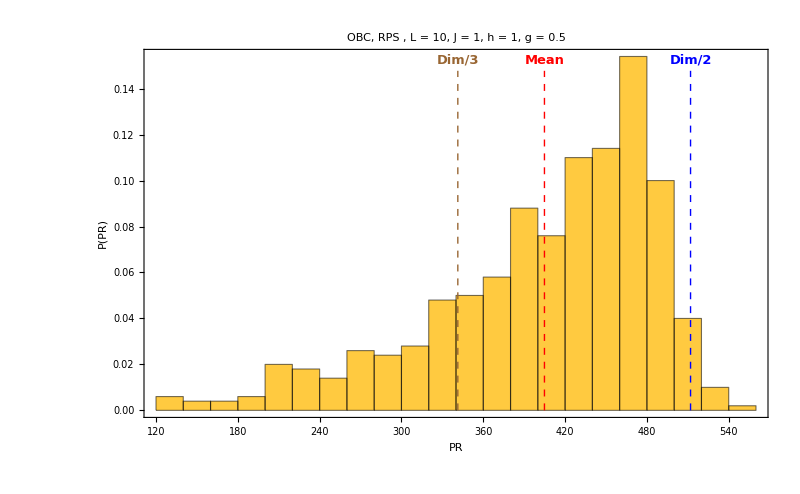

```mathematica
{bins,heights}=HistogramList[pr,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[pr,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["PR",25,Black],Style["P(PR)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[pr],0},{Mean[pr],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{(2^L)/2,0},{(2^L)/2,ymax*0.95}}]},{Brown,Dashed,Thick,Line[{{(2^L)/3,0},{(2^L)/3,ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[pr],ymax*0.98},{-1,0}],Text[Style["Dim/2",13,Blue,Bold],{(2^L)/2,ymax*0.98},{-1,0}],Text[Style["Dim/3",13,Brown,Bold],{(2^L)/3,ymax*0.98},{-1,0}]},PlotRange->All]
```

## Page value

```mathematica
haarstates=Table[haar[L],2000];
```

```mathematica
haarentropies=ParallelTable[With[{M=ArrayReshape[j,{2^(L/2),2^(L/2)}]},Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]],{j,haarstates}];
```

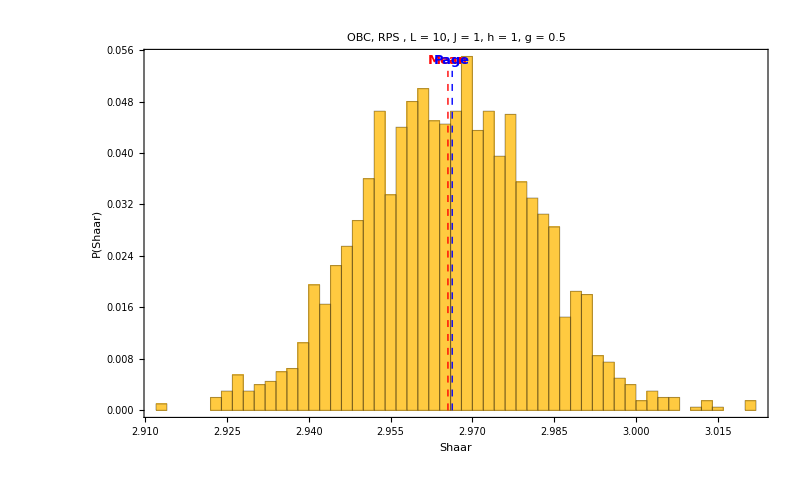

```mathematica
{bins,heights}=HistogramList[haarentropies,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[haarentropies,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Shaar",25,Black],Style["P(Shaar)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[haarentropies],0},{Mean[haarentropies],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[haarentropies],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

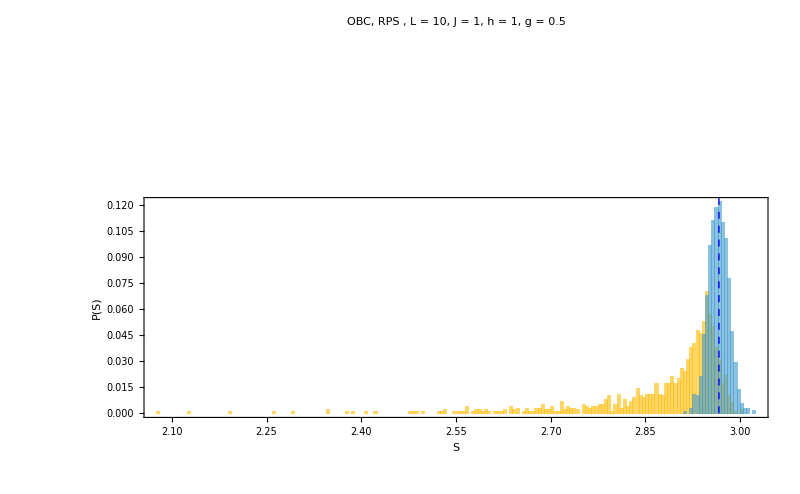

```mathematica
Histogram[{finalrps,haarentropies},"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["S",25,Black],Style["P(S)",25,Black]},ImageSize->800,Epilog->{{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*2.3}}]},Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*2.4},{-1,0}]},PlotRange->All]
```

## P(Svn) RPS, h = 1, g = 0.01

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,4,0.0050}];
tlist//Length
```

1001

```mathematica
productstatesfull=Table[RandomChainProductState[L],500];
```

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
DistributeDefinitions[evolvers,productstatesfull,new];
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

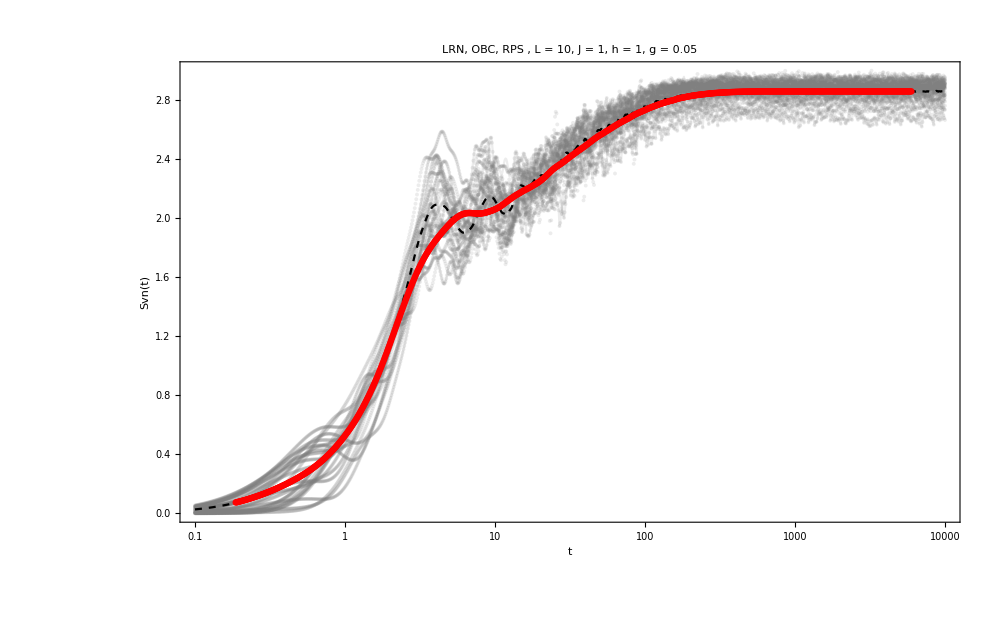

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

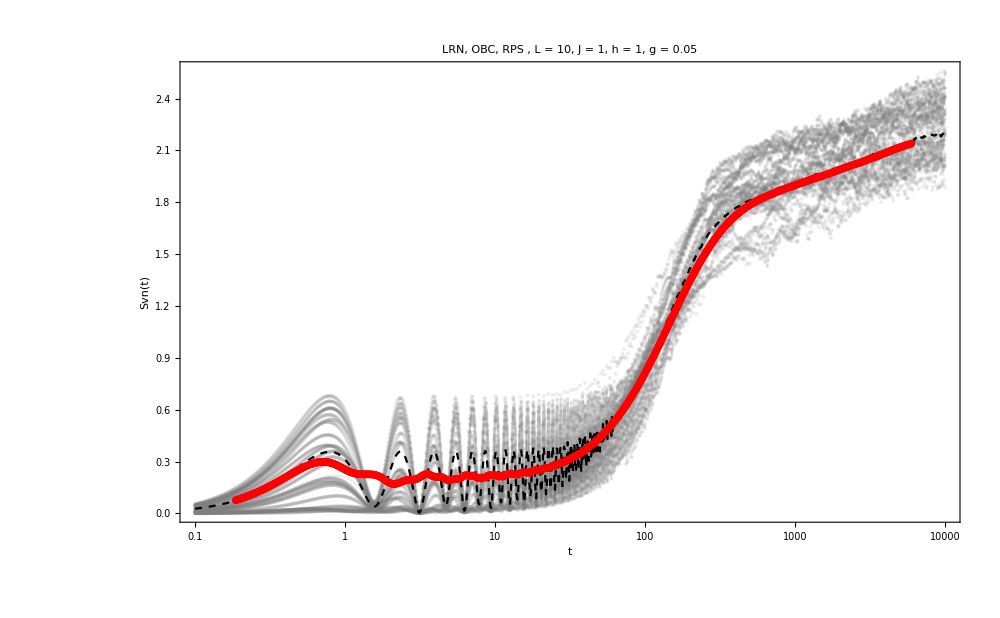

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

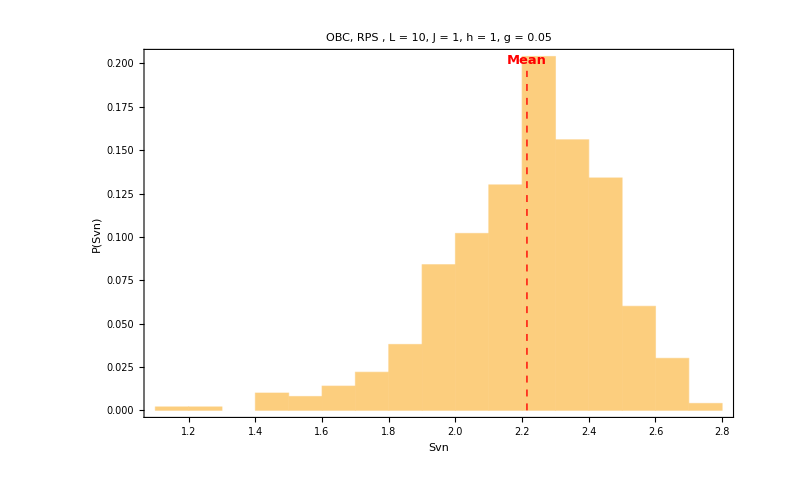

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
states=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
```

```mathematica
sdiagonal=ParallelTable[With[{M=ArrayReshape[j,{2^(L/2),2^(L/2)}]},Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]],{j,states}];
```

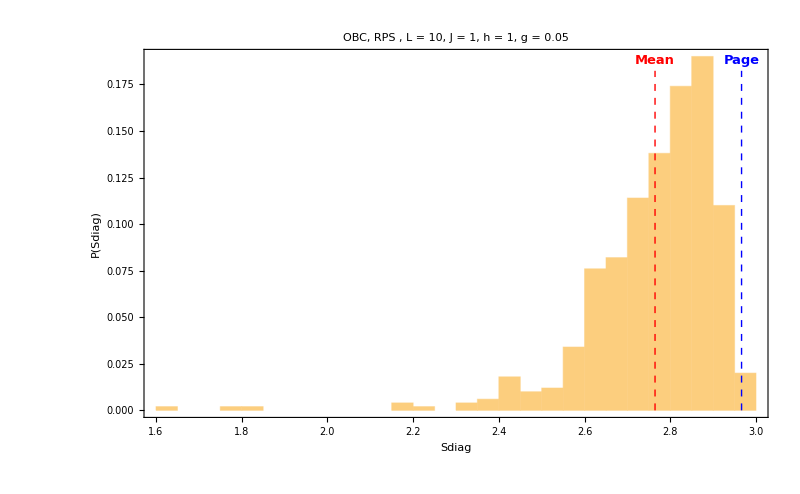

```mathematica
{bins,heights}=HistogramList[sdiagonal,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[sdiagonal,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Sdiag",25,Black],Style["P(Sdiag)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[sdiagonal],0},{Mean[sdiagonal],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[sdiagonal],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
cks=ParallelTable[Abs[Conjugate[allvecs].j]^2,{j,productstatesfull}];
```

```mathematica
pr=Table[1/Total[Abs[i]^2],{i,cks}];
```

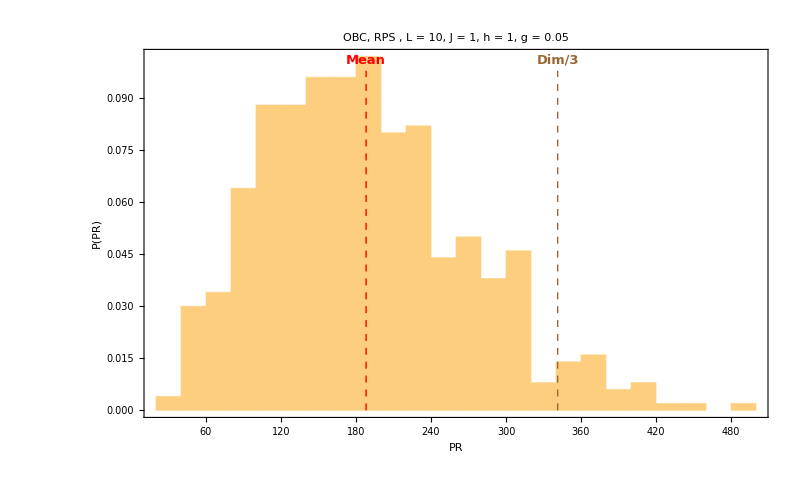

```mathematica
{bins,heights}=HistogramList[pr,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[pr,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["PR",25,Black],Style["P(PR)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[pr],0},{Mean[pr],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{(2^L)/2,0},{(2^L)/2,ymax*0.95}}]},{Brown,Dashed,Thick,Line[{{(2^L)/3,0},{(2^L)/3,ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[pr],ymax*0.98},{-1,0}],Text[Style["Dim/2",13,Blue,Bold],{(2^L)/2,ymax*0.98},{-1,0}],Text[Style["Dim/3",13,Brown,Bold],{(2^L)/3,ymax*0.98},{-1,0}]},PlotRange->All]
```

## P(Svn) Half Haar

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,4,0.0050}];
tlist//Length
```

1001

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],500];
```

```mathematica
evolvers=With[{phaseTable=Exp[-I Outer[Times,allvals,tlist]]},compiledEvolver[allvecs,phaseTable]];
```

```mathematica
DistributeDefinitions[evolvers,productstatesfull,new];
```

```mathematica
data=Module[{evolFunc=evolvers},
ParallelTable[With[{final=evolFunc[state]},
Map[new,Transpose[final]]],{state,productstatesfull}]];
```

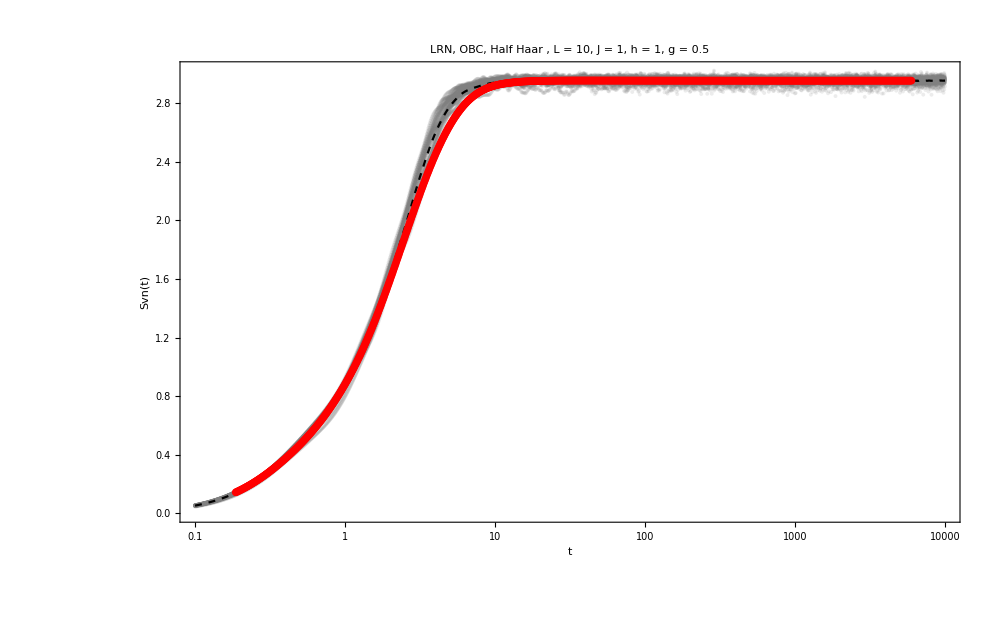

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

```mathematica
finalhalfhaar=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalhalfhaar,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

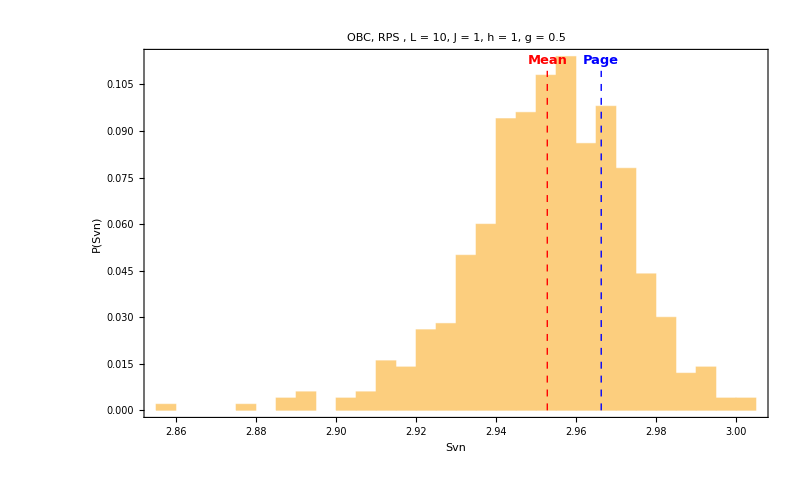

```mathematica
halfhaardis=Histogram[finalhalfhaar,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalhalfhaar],0},{Mean[finalhalfhaar],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalhalfhaar],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
states=ParallelTable[Conjugate[allvecs].j,{j,productstatesfull}];
```

```mathematica
sdiagonal=ParallelTable[With[{M=ArrayReshape[j,{2^(L/2),2^(L/2)}]},Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]],{j,states}];
```

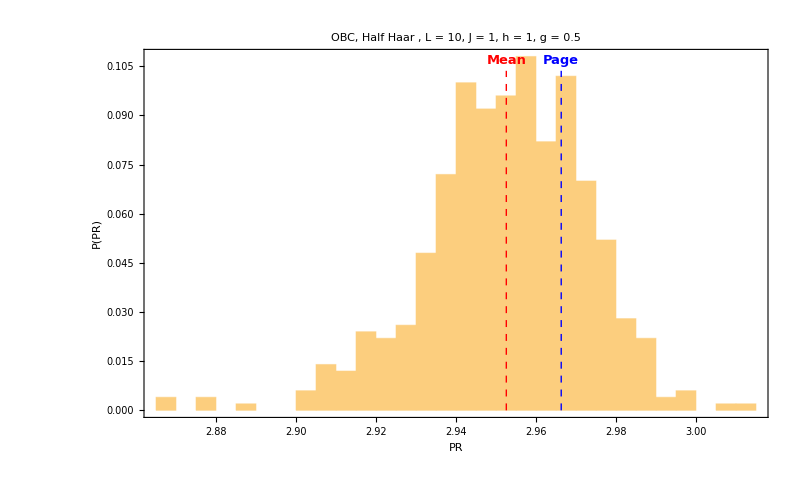

```mathematica
{bins,heights}=HistogramList[sdiagonal,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[sdiagonal,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["PR",25,Black],Style["P(PR)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[sdiagonal],0},{Mean[sdiagonal],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[sdiagonal],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

```mathematica
cks=ParallelTable[Abs[Conjugate[allvecs].j]^2,{j,productstatesfull}];
```

```mathematica
pr=Table[1/Total[Abs[i]^2],{i,cks}];
```

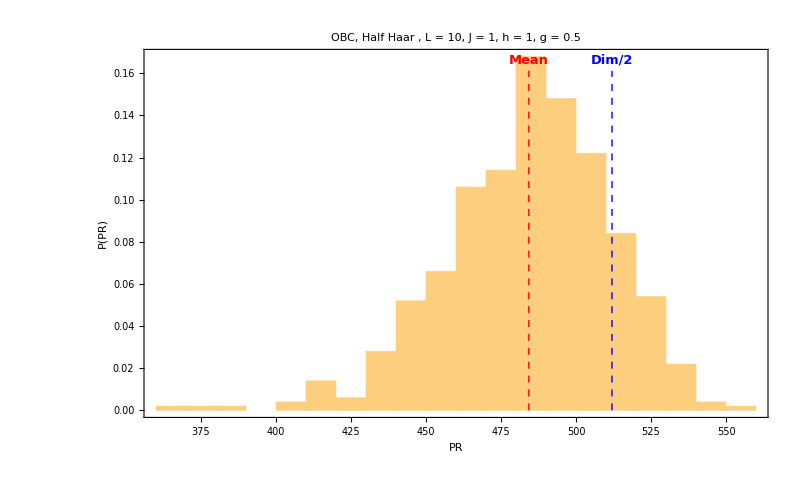

```mathematica
{bins,heights}=HistogramList[pr,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
Histogram[pr,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["PR",25,Black],Style["P(PR)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[pr],0},{Mean[pr],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{(2^L)/2,0},{(2^L)/2,ymax*0.95}}]},{Brown,Dashed,Thick,Line[{{(2^L)/3,0},{(2^L)/3,ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[pr],ymax*0.98},{-1,0}],Text[Style["Dim/2",13,Blue,Bold],{(2^L)/2,ymax*0.98},{-1,0}],Text[Style["Dim/3",13,Brown,Bold],{(2^L)/3,ymax*0.98},{-1,0}]},PlotRange->All]
```

# Test, faster parallelization

```mathematica
J=1;
h=1;
```

```mathematica
L=12;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
g=0.5;
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
```

```mathematica
neweven=ParallelTable[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=ParallelTable[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,10,0.0050}];
tlist//Length
```

2201

```mathematica
evolvers=compiledEvolver[allvecs,Exp[-I Outer[Times,allvals,tlist]]];
```

```mathematica
DistributeDefinitions[evolvers,VNentropy,new,L];
```

```mathematica
Clear[entanglementWorker];
entanglementWorker[state_]:=Module[{final},
final=evolvers[state];
Map[new,Transpose[final]]];
```

```mathematica
DistributeDefinitions[entanglementWorker];
```

```mathematica
productstatesfull=ParallelTable[RandomChainProductState[L],1000];
```

```mathematica
batchSize=50;
batches=Partition[productstatesfull,batchSize,batchSize,{1,1},{}];
```

```mathematica
data=Flatten[ParallelMap[(entanglementWorker/@#)&,batches],1];
```

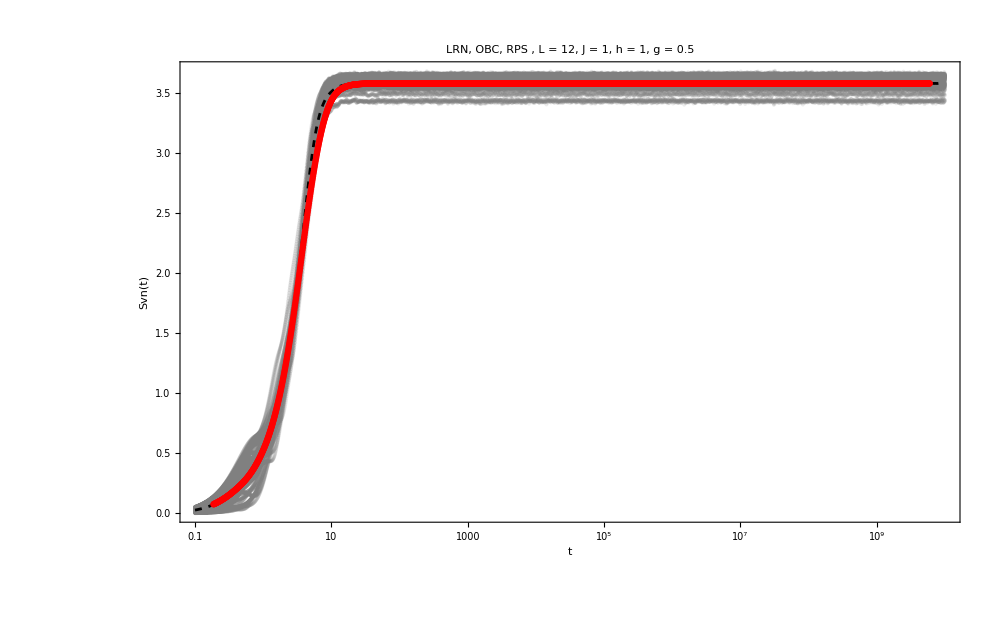

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

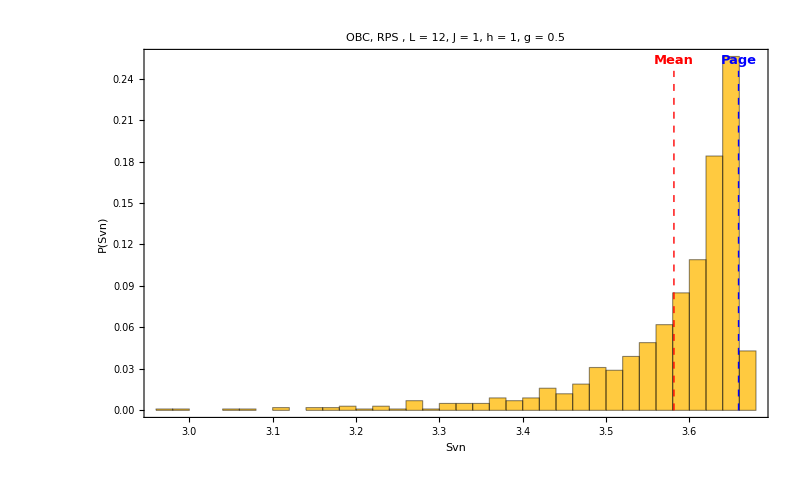

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

# Test, faster parallelization, import/export

```mathematica
J=1;
h=1;
```

```mathematica
L=14;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
g=0.5;
```

```mathematica
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
```

```mathematica
neweven=ParallelTable[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=ParallelTable[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]];
```

```mathematica
Clear[compiledEvolver];
compiledEvolver[eigenvec_,phaseTable_]:=With[{ev=Transpose[eigenvec],phases=phaseTable},
Compile[{{state,_Complex,1}},
Module[{ck,evolvedCoeffs,evolvedStates},
ck=Conjugate[eigenvec].state;
(*coefficients in eigenbasis*)
evolvedCoeffs=ck*phases;
(*time evolution and transformed back to site basis*)
evolvedStates=ev.evolvedCoeffs],CompilationTarget->"WVM",RuntimeOptions->{"EvaluateSymbolically"->False}
(*CompilationTarget->"C",Parallelization->True*)]];
```

```mathematica
tlist=Table[10^i,{i,-1,10,0.0050}];
tlist//Length
```

2201

```mathematica
phaseTable=Exp[-I Outer[Times,allvals,tlist]];
```

```mathematica
(*Exporting relevant data for later compilation*)
Export["eigenvecs_L_"<>ToString[L]<>".mx",allvecs];
Export["phaseTable_L_"<>ToString[L]<>".mx",phaseTable];
Export["eigenvals_L_"<>ToString[L]<>".mx",allvals];
```

```mathematica
ClearAll[eigenvecs,phaseTable,eigenvals];
ParallelEvaluate[ClearAll["Global`*"]];
```

```mathematica
CloseKernels[];
LaunchKernels[8];
```

```mathematica
ParallelEvaluate[{eigenvecs=Import["eigenvecs_L_14.mx"];
phaseTable=Import["phaseTable_L_14.mx"];
eigenvals=Import["eigenvals_L_14.mx"];
evolvers=compiledEvolver[eigenvecs,phaseTable];}];
```

Import::nffil: File eigenvecs.mx not found during Import.

General::stop: Further output of File `1` not found during `2`. will be suppressed during this calculation.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

Compile::cplist: Conjugate[$Failed] should be a tensor of type Integer, Real or Complex; evaluation will use the uncompiled function.

General::stop: Further output of `1` should be a tensor of type Integer, Real or Complex; evaluation will use the uncompiled function. will be suppressed during this calculation.

```mathematica
DistributeDefinitions[L,VNentropy,new];
```

```mathematica
Clear[entanglementWorker];
entanglementWorker[state_]:=Module[{final},final=evolvers[state];
Map[new,Transpose[final]]];
DistributeDefinitions[entanglementWorker];
```

```mathematica
productstatesfull=ParallelTable[RandomChainProductState[L],200];
```

```mathematica
batchSize=50;
batches=Partition[productstatesfull,batchSize,batchSize,{1,1},{}];
```

```mathematica
data=Flatten[ParallelMap[(entanglementWorker/@#)&,batches],1];
```

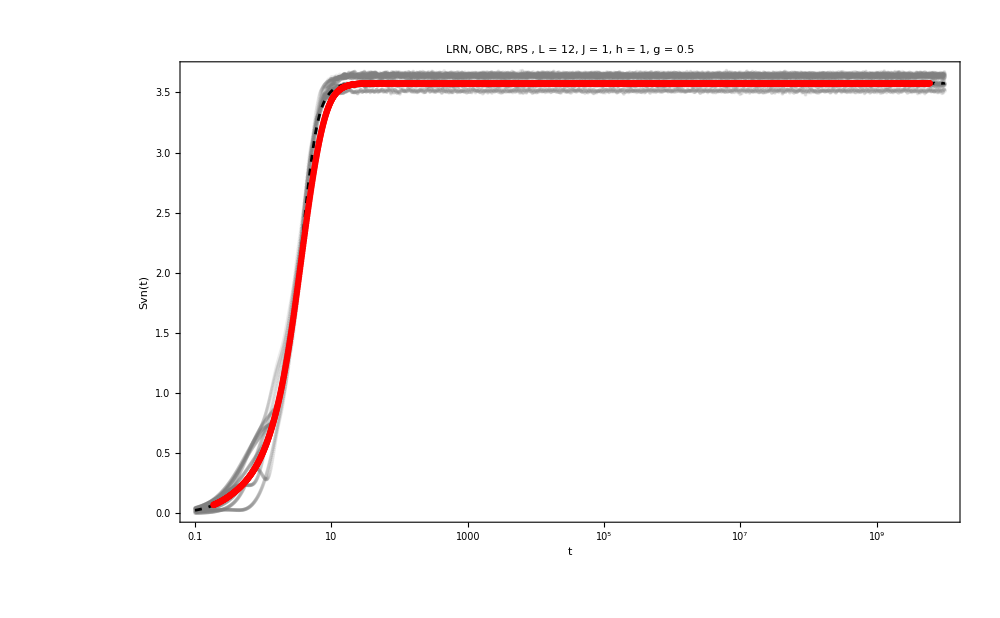

```mathematica
plot1=ListLogLinearPlot[Table[Transpose[{tlist,i}],{i,data[[1;;-1;;20]]}],PlotStyle->{Directive[Gray,Opacity[0.15]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
plot2=ListLogLinearPlot[{Transpose[{tlist,Mean[data]}],MovingAverage[Transpose[{tlist,Mean[data]}],100]},PlotStyle->{Directive[Black,Opacity[1],Dashed],Directive[Red,Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}];
Show[{plot1,plot2}]
```

```mathematica
finalrps=Table[i[[-1]],{i,data}];
{bins,heights}=HistogramList[finalrps,"FreedmanDiaconis","Probability"];
ymax=1.01*Max[heights];   (*5% taller than tallest bin*)
```

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```

-Graphics-

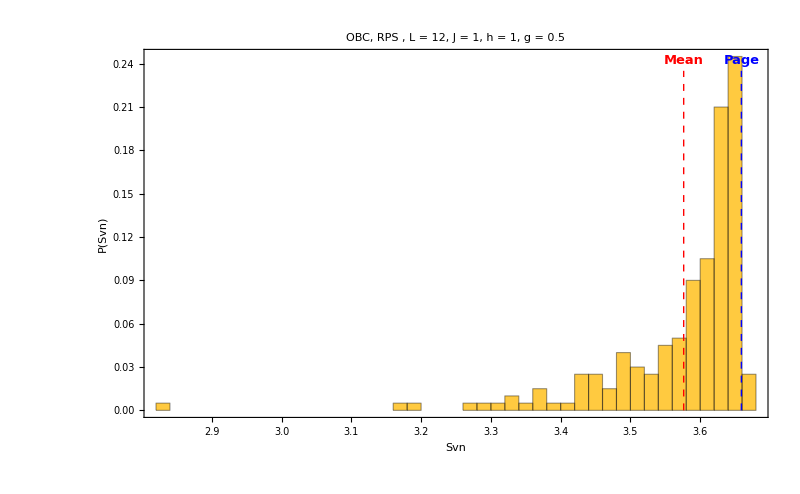

```mathematica
halfhaardis=Histogram[finalrps,"FreedmanDiaconis","Probability",PlotLabel->Style["OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[g],35,Black],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{Style["Svn",25,Black],Style["P(Svn)",25,Black]},ImageSize->800,Epilog->{{Red,Dashed,Thick,Line[{{Mean[finalrps],0},{Mean[finalrps],ymax*0.95}}]},{Blue,Dashed,Thick,Line[{{pageEntropy[L/2.,L/2.],0},{pageEntropy[L/2.,L/2.],ymax*0.95}}]},Text[Style["Mean",13,Red,Bold],{Mean[finalrps],ymax*0.98},{-1,0}],Text[Style["Page",13,Blue,Bold],{pageEntropy[L/2.,L/2.],ymax*0.98},{-1,0}]},PlotRange->All]
```